For the host-parasite system presented in the main text and all other model variants, we use standard adaptive dynamics techniques to investigate when a generalist parasite that can infect both hosts can “invade” (mathematically, this means investigating the stability of the equilibrium where the generalist is absent - the generalist can invade if this equilibrium is unstable). For all of the models we study, four assumptions remain constant: there are two potential hosts; infections occur due to contact between susceptible hosts and parasites in the environment; infected hosts shed parasites into the environment throughout the infection; generalist parasites have a reduced shedding rate compared to specialist parasites. 

The models differ in a number of ways that could affect the conclusions about the evolution of generalism. We explore models that differ in (1) the number of specialist parasites (either one or two); (2) the effect of parasitism on host population growth (dynamic versus constant population size); (3) the host-parasite contact process (parasites only come in contact with susceptible hosts; parasites come in contact with both susceptible and infected hosts; parasites come in contact with both host and non-host species); and (4) the parasite’s life cycle (direct versus trophic transmission).

### Case 1: Direct life cycle; one specialist parasite; parasite regulates host population size; active host seeking; avoidance of infected hosts

For this model, let S_1 and S_2 be the number of susceptible hosts of species 1 and 2, respectively. We will refer to these the “primary” and “secondary” hosts for simplicity. We assume that the “resident” parasite is a specialist on the primary host, and let I_(1r) be the number of primary hosts infected by the resident parasite. The “mutant” parasite is a generalist, and we let I_(1m) and I_(2m) be the number of primary and secondary hosts infected by the mutant parasite. We let P_r and P_m be the number of resident (specialist) and mutant (generalist) parasites in the environment.

In the absence of any infection, the primary and secondary hosts population sizes reach species-specific carrying capacities K_1 and K_2. Infection, however, induces mortality that depends on host traits, quantified by the species-specific mortality rates μ_1 and μ_2. Infected hosts shed parasites into the environment. The rate of shedding depends on host traits and whether the host is infected by a generalist or a specialist. Primary hosts infected by the specialist parasite shed parasites at the rate λ_1 , whereas primary hosts infected by the generalist parasite shed parasites at the reduced rate a λ_1. Secondary hosts infected by the generalist parasite shed at the rate a λ_2 (where λ_2 is the rate that a specialist parasite would be shed). We assume that the parasite controls the infection process and can detect whether a host is infected or not, so that parasites in the environment come in contact with susceptible hosts at the rate β. Finally, we assume that parasites are lost from the environment (whether due to death or washout) at the rate γ.

Note that we have assumed that specialist and generalist parasites differ only in the rate that they are shed from infected hosts, rather than assuming that they differ in transmission (β) or mortality (μ). The model for this system is given below:

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β S1 (Pr+Pm);
dS2dt=r2 (S2+I2m) (1-(S2+I2m)/K2)-β S2 Pm;
dI1rdt=β S1 Pr-μ1 I1r;
dPrdt=λ1 I1r-β S1 Pr-γ Pr;
dI1mdt=β S1 Pm-μ1 I1m;
dI2mdt=β S2 Pm-μ2 I2m;
dPmdt=a λ1 I1m+a λ2 I2m-β S1 Pm-β S2 Pm-γ Pm;
```

For an invasion analysis, we assume that the resident parasite comes to an ecological equilibrium with the host. Since it does not parasitize the second host, it will go to its carrying capacity: S_2=K_2. The density of the exploited host at equilibrium will be S_1=(γ μ_1)/(β (λ_1-μ_1)).

```mathematica
Eq=Solve[({dS1dt==0,dI1rdt==0,dPrdt==0}/.{I1m->0,Pm->0}),{S1,I1r,Pr}];
Eq[[4,1]]
```

S1→-(γ μ1)/(β (-λ1+μ1))

While evaluating the stability of the endemic equilibrium is somewhat challenging, it is obvious that, for there to be any chance for the endemic parasite equilibrium to be stable, the parasite extinction equilibrium must be unstable. This requires (β K (λ_1-μ))/(γ μ)>1. Notice that this is the reciprocal of the equilibrium host abundance at the endemic equilibrium, as expected.

```mathematica
Jres={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,Pr]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,Pr]},
{D[dPrdt,S1],D[dPrdt,I1r],D[dPrdt,Pr]}}/.{I1m->0,Pm->0};
(* Eigenvalues for the parasite-free equilibrium *)
Eigenvalues[Jres/.{I1r->0,Pr->0,S1->K1}]
```

{-r1,1/2 (-K1 β-γ-μ1-√((K1 β+γ+μ1)^2-4 (-K1 β λ1+K1 β μ1+γ μ1))),1/2 (-K1 β-γ-μ1+√((K1 β+γ+μ1)^2-4 (-K1 β λ1+K1 β μ1+γ μ1)))}

To determine whether the generalist parasite can invade, we need to examine the stability of the full system when the generalist parasite is absent (i.e., when I_(1,m)=0, I_(2,m)=0, and P_m=0). The Jacobian matrix for this is given below. Note that this matrix has a very simple structure: 
J=(J_s
0M
J_m)
This structure is actually quite convenient - J is an upper-triangular matrix, which means that its eigenvalues are given by the eigenvalues of J_s and J_m. The eigenvalues of J_s determine the stability of the endemic equilibria for the system with only the specialist parasite. By assumption, these eigenvalues are negative. Thus, we only need be concerned about the eigenvalues of J_m, which is the submatrix dealing with the equations for the generalist parasite.

```mathematica
J={{D[dS1dt,S1],D[dS1dt,S2],D[dS1dt,I1r],D[dS1dt,Pr],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,Pm]},
{D[dS2dt,S1],D[dS2dt,S2],D[dS2dt,I1r],D[dS2dt,Pr],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,Pm]},
{D[dI1rdt,S1],D[dI1rdt,S2],D[dI1rdt,I1r],D[dI1rdt,Pr],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,Pm]},
{D[dPrdt,S1],D[dPrdt,S2],D[dPrdt,I1r],D[dPrdt,Pr],D[dPrdt,I1m],D[dPrdt,I2m],D[dPrdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,S2],D[dI1mdt,I1r],D[dI1mdt,Pr],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,Pm]},
{D[dI2mdt,S1],D[dI2mdt,S2],D[dI2mdt,I1r],D[dI2mdt,Pr],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,Pm]},
{D[dPmdt,S1],D[dPmdt,S2],D[dPmdt,I1r],D[dPmdt,Pr],D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,Pm]}}/.{I1m->0,I2m->0,Pm->0};
MatrixForm[J]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1)-Pr β | 0 | -(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | -S1 β | -(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | 0 | -S1 β
0 | -(r2 S2)/K2+r2 (1-S2/K2) | 0 | 0 | 0 | -(r2 S2)/K2+r2 (1-S2/K2) | -S2 β
Pr β | 0 | -μ1 | S1 β | 0 | 0 | 0
-Pr β | 0 | λ1 | -S1 β-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | S1 β
0 | 0 | 0 | 0 | 0 | -μ2 | S2 β
0 | 0 | 0 | 0 | a λ1 | a λ2 | -S1 β-S2 β-γ)

However, rather than calculating these eigenvalues directly (which are difficult to interpret), we apply the next generation theorem.

```mathematica
F={{0,0,S1 β},{0,0,S2 β},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β+S2 β+γ}};
J[[5;;7,5;;7]]==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,-(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2),(√a √β √(S2 λ2 μ1+S1 λ1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2)}

If the largest of these eigenvalues is larger than 1, then the generalist-absent equilibrium is unstable. This is equivalent to requiring that (β (a λ_1-μ_1))/(γ μ_1)OverHat[S_1]+(β (a λ_1-μ_2))/(γ μ_2)OverHat[S_2]>1, where OverHat[S_1] and OverHat[S_2] are the equilibrium abundances of susceptible primary and secondary hosts when the generalist is absent. We can plug these equilibria into the stability condition. We define the left-hand side of this expression as R_0, the “invasion fitness” of the generalist parasite. Analogous to the canonical R_0 for an infectious disease, if R_0>1, the generalist will spread through the host population.

```mathematica
R0=((β (a λ1-μ1))/(γ μ1)S1+(β (a λ2-μ2))/(γ μ2)S2)/.{S1->-(γ μ1)/(β (-λ1+μ1)),S2->K2}
```

-(a λ1-μ1)/(-λ1+μ1)+(K2 β (a λ2-μ2))/(γ μ2)

We can explore how changing parameters of the model affect the magnitude of R_0 to see how these parameters affect the evolution of generalism. In particular, reducing the cost of generalism (increasing a) increases R_0; increasing the abundance of the secondary host (K_2) increases R_0; increasing the mortality induced by infection (μ_1 or μ_2) reduces R_0; increasing the parasite loss rate in the environment reduces R_0. None of these effects are surprising. However, in reality, many of these parameters are linked with one another by aspects of host physiology.

```mathematica
D[R0,a]//Simplify
D[R0,K2]
Simplify[D[R0,μ1]]
FullSimplify[D[R0,μ2]]
D[R0,γ]
```

λ1/(λ1-μ1)+(K2 β λ2)/(γ μ2)

(β (a λ2-μ2))/(γ μ2)

((-1+a) λ1)/(λ1-μ1)^2

-(a K2 β λ2)/(γ μ2^2)

-(K2 β (a λ2-μ2))/(γ^2 μ2)

In particular, carrying capacity, mortality rate, and shedding rate are all likely to be affected by host body size and temperature. Savage et al. 2004 suggested a scaling of 
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
for carrying capacity and mortality rate.

Hechinger 2012 suggested that within-host abundance correlates with body size and temperature. If we assume that shedding rate is a linear function of abundance, then 
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).
The difference in scaling for endoparasites and ectoparasites is because these two parasites utilize hosts differently: for endoparasites, abundance depends on host volume, whereas for ectoparasites, abundance depends on host surface area.

We assume that the only difference between the two hosts is in terms of body size. We let W be the mass of the primary host, and f W be the mass of the secondary host; without loss of generality, we assume that 0<f<1.

Notice that the derivatives of these expressions can be rewritten in terms of the expressions themselves:

```mathematica
K2=K0 Exp[Ε/(k T)] (f W)^(-3/4);
μ1=μ0 Exp[-Ε/(k T)] W^(-1/4);
μ2=μ0 Exp[-Ε/(k T)] (f W)^(-1/4);
λ1=λ0 Exp[-Ε/(k T)] W^(3/4);
λ2=λ0 Exp[-Ε/(k T)] (f W)^(3/4);
(* Derivatives with respect to mass *)
D[μ1,W]==-μ1/(4 W)//Simplify
D[λ1,W]==(3 λ1)/(4 W)//Simplify
D[K2,W]==(-3 K2)/(4 W)//Simplify
D[μ2,W]==-μ2/(4 W)//Simplify
D[λ2,W]==(3 λ2)/(4 W)//Simplify
(* Derivatives with respect to temperature *)
D[μ1,T]==Ε/(k T^2)μ1//Simplify
D[λ1,T]==Ε/(k T^2)λ1//Simplify
D[K2,T]==-Ε/(k T^2)K2//Simplify
Clear[μ2,K2,λ2,μ1,λ1]
```

True

True

True

«5 more identical outputs»

We can then study how R_0 is affected by changes in host body size or temperature for endoparasites and ectoparasites by differentiating R_0 with respect to host body size W and temperature T.

#### Endoparasites

For endoparasites, we find that increasing host body size always increases R_0 because dR_0/dW=((1-a) λ_1 μ_1)/(W(λ_1-μ_1))+(β K_2(a λ_2+3 μ_2))/(4 W γ μ_2), which is always positive.

```mathematica
(D[R0/.{λ1->λ1[W],μ1->μ1[W],λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==((1-a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)+(β K2[W] (a λ2[W]+3 μ2[W]))/(4 W γ μ2[W])//Simplify
```

True

We find that increasing temperature always decreases R_0 because dR_0/dT=(-β E K_2 (a λ_2-μ_2))/(k T^2 γ μ_2), which is always negative.

```mathematica
D[R0/.{λ1->λ1[T],μ1->μ1[T],λ2->λ2[T],μ2->μ2[T],K2->K2[T]},T]/.{μ1'[T]->Ε/(k T^2)μ1[T],λ1'[T]->Ε/(k T^2)λ1[T],K2'[T]->-Ε/(k T^2)K2[T],μ2'[T]->Ε/(k T^2)μ2[T],λ2'[T]->Ε/(k T^2)λ2[T]}//Simplify
```

(β Ε K2[T] (-a λ2[T]+μ2[T]))/(k T^2 γ μ2[T])

Thus, for endoparasites, we have that increasing the mass of the hosts (or making the masses more similar - since increasing f would increase the mass of the second host, it has the same sign as dR_0/dW) makes the evolution of generalism more likely, whereas increasing the temperature makes the evolution of generalism less likely.

#### Ectoparasites

For endoparasites, we find that increasing host body size has a more complicated effect. dR_0/dW=(2 (1-a) λ_1 μ_1)/(3 W(λ_1-μ_1))-(β K_2(a λ_2-9 μ_2))/(12 W γ μ_2); the sign of this expression depends on the sign of a λ_2-9 μ_2.

```mathematica
(D[R0/.{λ1->λ1[W],μ1->μ1[W],λ2->λ2[W],μ2->μ2[W],K2->K2[W]},W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W),λ2'[W]->(5 λ2[W])/(12 W)})==(2 (1-a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)-(β K2[W] (a λ2[W]-9 μ2[W]))/(12 W γ μ2[W])//Simplify
```

True

We find that this expression will be negative whenever W<27/f(μ_0/(a λ_0))^(3/2), meaning that the derivative dR_0/dW>0. So, if host body size is small, increasing host size will make it easier for a generalist to invade. However, as host body size gets larger, eventually dR_0/dW<0.

```mathematica
Solve[(a λ2[W]-9 μ2[W]/.{μ2[W]->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2[W]->λ0 Exp[-Ε/(k T)] (f W)^(5/12)})==0,W]
```

{{W→-(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))},{W→(27 μ0^(3/2))/(a^(3/2) f λ0^(3/2))}}

Increasing temperature has the same effect for an ectoparasite as an endoparasite.

### Case 2: Direct life cycle; two specialist parasites; parasite regulates host population size; active host seeking; avoidance of infected hosts

For this model, let S_1 and S_2 be the number of susceptible hosts of species 1 and 2, respectively. We will refer to these the “primary” and “secondary” hosts for simplicity. We assume that there are two “resident” parasites, one specializing on the primary host and the other specializing on the secondary host. We let I_(1r) and I_(2 r) be the number of primary and secondary hosts infected by the resident parasites. The “mutant” parasite is a generalist, and we let I_(1m) and I_(2m) be the number of primary and secondary hosts infected by the mutant parasite. We let P_1, P_2 and P_m be the number of resident (specialist) and mutant (generalist) parasites in the environment.

The model for this system is given below.

```mathematica
dS1dt=r1 (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β1 S1 (P1r+P12m);
dI1rdt=β1 S1 P1r-μ1 I1r;
dP1rdt=λ1 I1r-β1 S1 P1r-γ1 P1r;

dS2dt=r2 (S2+I2r+I2m) (1-(S2+I2r+I2m)/K2)-β2 S2 (P2r+P12m);
dI2rdt=β2 S2 P2r-μ2 I2r;
dP2rdt=λ2 I2r-β2 S2 P2r-γ2 P2r;

dI1mdt=β1 S1 P12m-μ1 I1m;
dI2mdt=β2 S2 P12m-μ2 I2m;
dP12mdt=a λ1 I1m+a λ2 I2m-β1 S1 P12m-β2 S2 P12m-γ P12m;
```

Note that the specialist parasites do not have any interaction with one another (i.e., the dynamics of S_1,I_(1r), and P_1 do not depend on S_2,I_(2r,)or P_2). Since, for an invasion analysis, we assume that the resident parasites come to an ecological equilibrium with their hosts, we can solve for these equilibria easily, finding that S_1=(γ_1 μ_1)/(β_1 (λ_1-μ_1)) and S_2=(γ_2 μ_2)/(β_2(λ_2-μ_2)).

```mathematica
Eq=Solve[({dS1dt==0,dS2dt==0,dI1rdt==0,dI2rdt==0,dP1rdt==0,dP2rdt==0}/.{I1m->0,I2m->0,P12m->0}),{S1,S2,I1r,I2r,P1r,P2r}];
Eq[[13,1;;2]]
```

{S1→-(γ1 μ1)/(β1 (-λ1+μ1)),S2→-(γ2 μ2)/(β2 (-λ2+μ2))}

To determine whether the generalist parasite can invade, we need to examine the stability of the full system when the generalist parasite is absent (i.e., when I_(1m)=0, I_(2m)=0, and P_(12,m)=0). The Jacobian matrix for this is given below. Note that this matrix has a very simple structure: 
J=(J_1
0
00
J_2
0M_1
M_2
J_m)
This structure is actually quite convenient - J is an upper-triangular matrix, which means that its eigenvalues are given by the eigenvalues of J_1, J_2, and J_m. The eigenvalues J_1 and J_2 determine the stability of the endemic equilibria for the two specialist parasite. By assumption, these eigenvalues are negative. Thus, we only need be concerned about the eigenvalues of J_m, which is the submatrix dealing with the equations for the generalist parasite.

```mathematica
J={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,P1r],D[dS1dt,S2],D[dS1dt,I2r],D[dS1dt,P2r],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,P12m]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,S2],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,S2],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dS2dt,S1],D[dS2dt,I1r],D[dS2dt,P1r],D[dS2dt,S2],D[dS2dt,I2r],D[dS2dt,P2r],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,P12m]},
{D[dI2rdt,S1],D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,S2],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,S1],D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,S2],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,S1],D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,S2],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,S1],D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,S2],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,S1],D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,S2],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J[[1;;3,1;;3]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1)-P1r β1 | -(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | -S1 β1
P1r β1 | -μ1 | S1 β1
-P1r β1 | λ1 | -S1 β1-γ1)

```mathematica
MatrixForm[J[[1;;3,4;;6]]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[1;;3,7;;9]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | 0 | -S1 β1
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[4;;6,1;;3]]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[4;;6,4;;6]]]
```

(-(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2)-P2r β2 | -(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2) | -S2 β2
P2r β2 | -μ2 | S2 β2
-P2r β2 | λ2 | -S2 β2-γ2)

```mathematica
MatrixForm[J[[4;;6,7;;9]]]
```

(0 | -(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2) | -S2 β2
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[1;;3,7;;9]]]
```

(-(r1 (I1r+S1))/K1+r1 (1-(I1r+S1)/K1) | 0 | -S1 β1
0 | 0 | 0
0 | 0 | 0)

```mathematica
MatrixForm[J[[4;;6,7;;9]]]
```

(0 | -(r2 (I2r+S2))/K2+r2 (1-(I2r+S2)/K2) | -S2 β2
0 | 0 | 0
0 | 0 | 0)

The eigenvalues of this matrix determine the stability of the generalist-absent system.

```mathematica
MatrixForm[J[[7;;9,7;;9]]]
```

(-μ1 | 0 | S1 β1
0 | -μ2 | S2 β2
a λ1 | a λ2 | -S1 β1-S2 β2-γ)

Applying the next generation theorem, we find that the stability of the system depends on the magnitude of (√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2) - if this is greater than 1, then the generalist-absent equilibrium is unstable and the generalist can invade.

```mathematica
F={{0,0,S1 β1},{0,0,S2 β2},{a λ1,a λ2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β1+S2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]
```

{0,-(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2),(√a √(S2 β2 λ2 μ1+S1 β1 λ1 μ2))/(√(S1 β1+S2 β2+γ) √μ1 √μ2)}

This condition can be rewritten as
((a λ_1-μ_1)β_1)/(μ_1 γ)OverHat[S_1]+((a λ_2-μ_2)β_2)/(μ_2 γ)OverHat[S_2]>1,
where OverHat[S_1] and OverHat[S_2] are the endemic equilibrium reached when only the specialist parasites are present. Interestingly, ((a λ_1-μ_1)β_1)/(μ_1 γ) is the reciprocal of the equilibrium abundance of the first host if the generalist parasite was the only parasite in the system and it only infected the first host; similarly, ((a λ_2-μ_2)β_2)/(μ_2 γ) is the reciprocal of the equilibrium abundance of the second host, if the generalist parasite was the only parasite in the system and it only infected the second host. Plugging in the equilibrium values for OverHat[S_1] and OverHat[S_2], the invasion condition simplifies to
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1.

Notice that there are only three factors that influence whether a generalist parasite can invade or not: the cost of generalism a, the shedding rates λ_1 and λ_2, and the host mortality rates μ_1 and μ_2. In this model, the abundance of the hosts matters not at all, contrary to simple verbal theories for the evolution of generalism. Of course, this is because we assume that the parasite regulates the host population size. If that is not the case, we have a different model, one in which parasites can move hosts into an infected class, but do not cause mortality.

Regardless, we can use a similar analysis to study how changing the host body size or temperature will affect the ability of the generalist parasite to invade. Notice that because increasing the mass of the hosts increases shedding rates and decreases mortality rates, increasing host body size will still increase the likelihood that the generalist can invade, for both endoparasites and ectoparasites.

Effect of increasing body size for a generalist endoparasite:

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W]),W]/.{K1'[W]->(-3 K1[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
Simplify[D[(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)}]
```

-((-1+a) λ1[W] μ1[W])/(W (λ1[W]-μ1[W])^2)

-((-1+a) λ2[W] μ2[W])/(W (λ2[W]-μ2[W])^2)

Effect of increasing body size for a generalist ectoparasite:

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W]),W]/.{K1'[W]->(-3 K1[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W)}]
Simplify[D[(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{K2'[W]->(-3 K2[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]
```

-(2 (-1+a) λ1[W] μ1[W])/(3 W (λ1[W]-μ1[W])^2)

-(2 (-1+a) λ2[W] μ2[W])/(3 W (λ2[W]-μ2[W])^2)

However, for both endoparasites and ectoparasites, the invasion fitness is independent of temperature (because shedding rate and mortality rate scale with temperature in the same way):

```mathematica
D[(a λ1-μ1)/(λ1-μ1)+(a λ2-μ2)/(λ2-μ2)/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)},T]//Simplify
```

0

### Case 3: Direct life cycle; two specialist parasites; constant host population size; active host seeking; avoidance of infected hosts

For this model, we assume that the primary and secondary host population sizes are constant at K_1 and K_2, respectively. As such, we do not need to keep track of the dynamics of both susceptible and infected hosts - we can simply track the prevalence of infection. We define I_(1r) and I_(2r) as the fraction of primary and secondary hosts infected by the specialist parasites, respectively. 

The dynamics of parasites in the environment are governed by shedding and loss, as before. The rate of shedding depends on the number of infected hosts, e.g., I_(1r)K_1. Similarly, loss due to contact with susceptible hosts depends on the number of susceptible hosts, e.g., (1-I_(1r)-I_(1m))K_1. 

The model is given below:

```mathematica
dI1rdt=β1 (1-I1r-I1m) P1r-μ1 I1r;
dP1rdt=λ1 I1r K1-β1 (1-I1r-I1m) K1 P1r -γ P1r;

dI2rdt=β2 (1-I2r-I2m) P2r-μ2 I2r;
dP2rdt=λ2 I2r K2-β2 (1-I2r-I2m) K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-I1m) P12m-μ1 I1m;
dI2mdt=β2 (1-I2r-I2m) P12m-μ2 I2m;
dP12mdt=a λ1 I1m K1 +a λ2 I2m K2 -β1 (1-I1r-I1m) K1  P12m-β2 (1-I2r-I2m) K2 P12m-γ P12m;
```

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= 1 -(γ μ_1)/(β_1 K_1(λ_1-μ_1)) and I_(2,r)= 1-(γ μ_2)/(β_2 K_2(λ_2-μ_2)), implying that the equilibrium number of susceptibles are (γ μ_1)/(β_1 K_1(λ_1-μ_1)) and (γ μ_2)/(β_2 K_2(λ_2-μ_2)).

```mathematica
Eq=Solve[({dI1rdt==0,dP1rdt==0,dI2rdt==0,dP2rdt==0}/.{I1m->0,I2m->0}), {I1r,P1r,I2r,P2r}]//Simplify;
Eq[[4]]
```

{I1r→(K1 β1 λ1-K1 β1 μ1-γ μ1)/(K1 β1 λ1-K1 β1 μ1),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 γ),I2r→(K2 β2 λ2-K2 β2 μ2-γ μ2)/(K2 β2 λ2-K2 β2 μ2),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 γ)}

The Jacobian matrix for the full system is:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 P1r β1+K1 λ1 | -(1-I1r) K1 β1-γ | 0 | 0 | K1 P1r β1 | 0 | 0
0 | 0 | -P2r β2-μ | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 P2r β2+K2 λ2 | -(1-I2r) K2 β2-γ | 0 | K2 P2r β2 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -(1-I1r) K1 β1-(1-I2r) K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1.

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,(1-I1r) K1 β1+(1-I2r)K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2),(√a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√((-1+I1r) K1 β1+(-1+I2r) K2 β2-γ) √μ1 √μ2)}

This condition can be simplified to
(β_1 K_1(a λ_1-μ_1))/(γ μ_1)(1-I_(1,r))+(β_2 K_2(a λ_2-μ_2))/(γ μ_2)(1-I_(2,r))>1,
which, after plugging in the generalist-free endemic equilibria for I_(1,r) and I_(2,r), simplifies to 
(a λ_1-μ_1)/(λ_1-μ_1)+(a λ_2-μ_2)/(λ_2-μ_2)>1

```mathematica
Simplify[(β1 K1(a λ1-μ1))/(γ μ1)(1-I1r)/.{I1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(K1 β1 λ1-K1 β1 μ1)}]
Simplify[(β2 K2(a λ2-μ2))/(γ μ2)(1-I2r)/.{I2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(K2 β2 λ2-K2 β2 μ2)}]
```

(a λ1-μ1)/(λ1-μ1)

(a λ2-μ2)/(λ2-μ2)

We can again see how changing host body size and temperature will affect invasion by looking at the derivatives of the invasion condition with respect to body size and temperature, after substituting in the allometric scaling relationships. Note that now you have a contravailing pressure of increasing body size on invasion fitness for the generalist: increasing host body size increases shedding rate, but decreases carrying capacity.

For an endoparasite, the derivative of the invasion fitness with respect to host body size is always positive because dR_0/dW=(1-a)/W((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
(D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W] -μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)})==(1-a)/W((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

Similarly, for an ectoparasite, the derivative of the invasion fitness with respect to host body size is always positive beacuse dR_0/dW=(2 (1-a))/(3 W)((λ_1 μ_1)/(λ_1-μ_1)^2+(λ_2 μ_2)/(λ_2-μ_2)^2).

```mathematica
Simplify[D[(a λ1[W]-μ1[W])/(λ1[W]-μ1[W])+(a λ2[W]-μ2[W])/(λ2[W]-μ2[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(5 λ1[W])/(12 W),μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(5 λ2[W])/(12 W)}]==(2 (1-a))/(3 W)((λ1[W] μ1[W])/(λ1[W]-μ1[W])^2+(λ2[W] μ2[W])/(λ2[W]-μ2[W])^2)//Simplify
```

True

For both endoparasites and ectoparasites, the derivative of the invasion fitness with respect to temperature is zero, as before.

```mathematica
D[(a λ1[T] -μ1[T])/(λ1[T] -μ1[T])+(a λ2[T] -μ2[T])/(λ2[T] -μ2[T]),T]/.{μ2'[T]->(Ε μ2[T])/(k T^2),λ2'[T]->(Ε λ2[T])/(k T^2),μ1'[T]->(Ε μ1[T])/(k T^2),λ1'[T]->(Ε λ1[T])/(k T^2)}//Simplify
```

0

### Case 4: Direct life cycle; two specialist parasites; constant host population size; active host seeking; no avoidance of infected hosts

The only change with the model above involves the loss of parasites due to contact with hosts. Since the parasite cannot determine whether a host is infected or not, the loss rate is, e.g., β K_1. Parasite consumption by an infected individual has no effect on infection status; if the parasite ends up in an already-infected host, it is simply lost from the system.

```mathematica
dI1rdt=β1 (1-I1r-I1m) P1r-μ1 I1r;
dP1rdt=λ1 I1r K1-β1 K1 P1r-γ P1r;

dI2rdt=β2 (1-I2r-I2m) P2r-μ2 I2r;
dP2rdt=λ2 I2r K2-β2 K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-I1m) P12m-μ1 I1m;
dI2mdt=β2 (1-I2r-I2m) P12m-μ2 I2m;
dP12mdt=a λ1 I1m K1 +a λ2 I2m K2 -β1 K1 P12m-β2 K2 P12m-γ P12m;
```

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= 1-((K1 β1+γ) μ1)/(K1 β1 λ1) and I_(2,r)= 1-((K2 β2+γ) μ2)/(K2 β2 λ2).

```mathematica
Solve[({dI1rdt==0,dP1rdt==0,dI2rdt==0,dP2rdt==0}/.{I1m->0,I2m->0}), {I1r,P1r,I2r,P2r}]//Simplify
```

{{I1r→0,P1r→0,I2r→0,P2r→0},{I1r→1-((K1 β1+γ) μ1)/(K1 β1 λ1),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ)),I2r→0,P2r→0},{I1r→0,P1r→0,I2r→1-((K2 β2+γ) μ2)/(K2 β2 λ2),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))},{I1r→1-((K1 β1+γ) μ1)/(K1 β1 λ1),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ)),I2r→1-((K2 β2+γ) μ2)/(K2 β2 λ2),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))}}

Skipping ahead to the calculation of the Jacobian for the full system:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 λ1 | -K1 β1-γ | 0 | 0 | 0 | 0 | 0
0 | 0 | -P2r β2-μ2 | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 λ2 | -K2 β2-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -K1 β1-K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -K1 β1-K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1. This expression simplifies to

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,K1 β1+K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-((ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)),(ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)}

Notice that if you square the second eigenvalue, you get a positive real number - this is R_0 for the generalist for this system.

```mathematica
(-((ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)))^2
```

-((a ((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/((K1 β1+K2 β2+γ) μ1 μ2))

If you plug in the equilibrium values of I_(1r) and I_(2r), you end up with a very simple expression, which is the cost of generalism multiplied by 1 plus the probability that a parasite in the environment is lost rather than consumed (γ/(β_1 K_1+β_2 K_2+γ)).

```mathematica
Simplify[-((a ((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/((K1 β1+K2 β2+γ) μ1 μ2))/.{I1r->1-((K1 β1+γ) μ1)/(K1 β1 λ1),I2r->1-((K2 β2+γ) μ2)/(K2 β2 λ2)}]==a(1+γ/(β1 K1+β2 K2+γ))//Simplify
```

True

For an endoparasite, we again see that increasing body size increases the magnitude of the invasion exponent (because increasing body size decreases the carrying capacity, thereby increasing the probability that a parasite in the environment will be lost rather than consumed - this increases the benefit to being a generalist).

```mathematica
Simplify[D[a(1+γ/(β1 K1[W]+β2 K2[W]+γ)),W]/.{K1'[W]->(-3 K1[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)}]
```

(3 a γ (β1 K1[W]+β2 K2[W]))/(4 W (γ+β1 K1[W]+β2 K2[W])^2)

This is true for endoparasites as well:

```mathematica
Simplify[D[a(1+γ/(β1 K1[W]+β2 K2[W]+γ)),W]/.{K1'[W]->(-5 K1[W])/(12 W),K2'[W]->(-5 K2[W])/(12 W)}]
```

(5 a γ (β1 K1[W]+β2 K2[W]))/(12 W (γ+β1 K1[W]+β2 K2[W])^2)

Interestingly, now increasing temperature actually increases the likelihood that the generalist parasite can invade - warmer temperatures decrease carrying capacity, thereby making it more likely that a parasite in the environment ends up not infecting any host.

```mathematica
Simplify[D[a(1+γ/(β1 K1[T]+β2 K2[T]+γ)),T]/.{K1'[T]->-(Ε K1[W])/(k T^2),K2'[T]->-(Ε K2[W])/(k T^2)}]
```

(a γ Ε (β1 K1[W]+β2 K2[W]))/(k T^2 (γ+β1 K1[T]+β2 K2[T])^2)

### Case 5: Direct life cycle; two specialist parasites; constant host population size; passive host seeking; no avoidance of infected hosts

For this model, we assume that both hosts remove both parasites from the environment, but only compatible host-parasite pairs trigger infection. That is, specialists on the primary host are also “consumed” by secondary hosts (and vice versa). Intuively, you would expect this to increase the likelihood that a generalist can invade.

```mathematica
dI1rdt=β1 (1-I1r-I1m) P1r-μ1 I1r;
dP1rdt=λ1 I1r K1-β1 K1 P1r-β2 K2 P1r -γ P1r;

dI2rdt=β2 (1-I2r-I2m) P2r-μ2 I2r;
dP2rdt=λ2 I2r K2-β1 K1 P2r-β2 K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-I1m) P12m-μ1 I1m;
dI2mdt=β2 (1-I2r-I2m) P12m-μ2 I2m;
dP12mdt=a λ1 I1m K1 +a λ2 I2m K2 -β1 K1  P12m-β2 K2 P12m-γ P12m;
```

In the absence of the generalist parasite, the equilibrium prevalences of infection are I_(1,r)= (K1 β1 (λ1-μ1)-(K2 β2+γ) μ1)/(K1 β1 λ1) and I_(2,r)= (K2 β2 (λ2-μ2)-(K1 β1+γ) μ2)/(K2 β2 λ2).

```mathematica
Solve[({dI1rdt==0,dP1rdt==0,dI2rdt==0,dP2rdt==0}/.{I1m->0,I2m->0}), {I1r,P1r,I2r,P2r}]//Simplify
```

{{I1r→0,P1r→0,I2r→0,P2r→0},{I1r→(K1 β1 (λ1-μ1)-(K2 β2+γ) μ1)/(K1 β1 λ1),P1r→(K1 β1 (λ1-μ1)-(K2 β2+γ) μ1)/(β1 (K1 β1+K2 β2+γ)),I2r→0,P2r→0},{I1r→0,P1r→0,I2r→(K2 β2 (λ2-μ2)-(K1 β1+γ) μ2)/(K2 β2 λ2),P2r→(K2 β2 (λ2-μ2)-(K1 β1+γ) μ2)/(β2 (K1 β1+K2 β2+γ))},{I1r→(K1 β1 (λ1-μ1)-(K2 β2+γ) μ1)/(K1 β1 λ1),P1r→(K1 β1 (λ1-μ1)-(K2 β2+γ) μ1)/(β1 (K1 β1+K2 β2+γ)),I2r→(K2 β2 (λ2-μ2)-(K1 β1+γ) μ2)/(K2 β2 λ2),P2r→(K2 β2 (λ2-μ2)-(K1 β1+γ) μ2)/(β2 (K1 β1+K2 β2+γ))}}

Skipping ahead to the calculation of the Jacobian for the full system:

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,P1r],D[dI1rdt,I2r],D[dI1rdt,P2r],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dP1rdt,I1r],D[dP1rdt,P1r],D[dP1rdt,I2r],D[dP1rdt,P2r],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dI2rdt,I1r],D[dI2rdt,P1r],D[dI2rdt,I2r],D[dI2rdt,P2r],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP2rdt,I1r],D[dP2rdt,P1r],D[dP2rdt,I2r],D[dP2rdt,P2r],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dI1mdt,I1r],D[dI1mdt,P1r],D[dI1mdt,I2r],D[dI1mdt,P2r],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,I1r],D[dI2mdt,P1r],D[dI2mdt,I2r],D[dI2mdt,P2r],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,I1r],D[dP12mdt,P1r],D[dP12mdt,I2r],D[dP12mdt,P2r],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{I1m->0,I2m->0,P12m->0};
MatrixForm[J]
```

(-P1r β1-μ1 | (1-I1r) β1 | 0 | 0 | -P1r β1 | 0 | 0
K1 λ1 | -K1 β1-K2 β2-γ | 0 | 0 | 0 | 0 | 0
0 | 0 | -P2r β2-μ2 | (1-I2r) β2 | 0 | -P2r β2 | 0
0 | 0 | K2 λ2 | -K1 β1-K2 β2-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | (1-I1r) β1
0 | 0 | 0 | 0 | 0 | -μ2 | (1-I2r) β2
0 | 0 | 0 | 0 | a K1 λ1 | a K2 λ2 | -K1 β1-K2 β2-γ)

As before, this has a upper block triangular structure, and whether the generalist can invade is entirely determined by the bottom left submatrix:

```mathematica
MatrixForm[J[[5;;7,5;;7]]]
```

(-μ1 | 0 | (1-I1r) β1
0 | -μ2 | (1-I2r) β2
a K1 λ1 | a K2 λ2 | -K1 β1-K2 β2-γ)

Applying the next generation matrix theorem, the generalist will be able to invade if the eigenvalue is greater than 1.

```mathematica
F={{0,0,(1-I1r) β1},{0,0,(1-I2r) β2},{a λ1 K1,a λ2 K2,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,K1 β1+K2 β2+γ}};
Eigenvalues[Dot[F,Inverse[V]]]//Simplify
```

{0,-((ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)),(ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)}

Squaring the second eigenvalue yields a positive real number, which is R_0 for the generalist in this model:

```mathematica
(-((ⅈ √a √((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/(√(K1 β1+K2 β2+γ) √μ1 √μ2)))^2
```

-((a ((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/((K1 β1+K2 β2+γ) μ1 μ2))

Interestingly, if you plug in the equilibria, you end up with a very simple expression, which is that the only thing that matters is the cost of generalism. Thus, host body size and temperature have no effect on anything in this model.

```mathematica
-((a ((-1+I2r) K2 β2 λ2 μ1+(-1+I1r) K1 β1 λ1 μ2))/((K1 β1+K2 β2+γ) μ1 μ2))/.{I1r->(K1 β1 (λ1-μ1)-(K2 β2+γ) μ1)/(K1 β1 λ1),I2r->(K2 β2 (λ2-μ2)-(K1 β1+γ) μ2)/(K2 β2 λ2)}//Simplify
```

2 a

### Case 6: Trophic transmission; one specialist parasite; parasites regulate definitive host population sizes; active seeking of intermediate hosts; avoidance of infected intermediate hosts

Let D_1 and D_2 be two definitive hosts and N be prey of both and the intermediate host. One touchy bit is how to deal with the effect of ingestion on both the dynamics of predator (the definitive host) and prey (the intermediate host). One possibility is that infection is embedded within a classic predator-prey model, where both predator and prey growth are impacted by one another. Such a model is quite different from the direct life cycle model studied in the main text, and is also very difficult to analyze. A second possibility is that prey density is constant; in this model you cannot assume that predator growth is entirely determined by prey ingestion (as in a classic predator-prey model) because the predator population will either grow or decay exponentially. We consider two possibilities: that the predator population is growing logistically or that it is constant. 

Here we assume that the intermediate host (the prey) has a constant population size. We let N_T be the total population size, and N_(I,r) and N_(I,m) be the abundance of intermedate host infected with the resident (specialist) and mutant (generalist) parasites, respectively. We don’t need to track the number of susceptible intermediate hosts. The two definitive hosts both grow logistically in the absence of infection, with no direct effect of prey ingestion on their growth rate. One way to justify this assumption is to assume that the predators are eating lots of different prey items, so that their dynamics are largely independent of this particular prey item. However, infection is assumed to have an effect on the growth of the definitive host. We let D_(1,S) and D_(2,S) to be the number of primary and secondary definitive hosts that are susceptible to infection; D_(1,I,r) is the number of primary definitive hosts infected by the specialist (resident) parasite; we assume that the secondary definitive host is not infected by its own specialist parasite. D_(1,I,m) and D_(2,I,m) are the numbers of primary and secondary definitive hosts infected by the generalist (mutant) parasite. Definitive hosts shed parasite back into the environment, with P_r and P_m the abundance of specialist and generalist in the environment. These parasites are consumed by the intermediate host, which can then transmit the parasite to the definitive host upon ingestion.

Note that there is no need to consider active vs. passive host seeking here, as there is only a single intermediate host that is assumed to contact parasites in the environment. 

The full system is given below.

```mathematica
dNirdt=β (NT-Nir-Nim) Pr-a1 (D1s+D1ir+D1im)Nir-a2(D2s+D2im) Nir;
dNimdt=β (NT-Nir-Nim) Pm-a1 (D1s+D1ir+D1im)Nim-a2 (D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;
dPrdt=λ1 D1ir-β (NT-Nir-Nim) Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-Nir-Nim) Pm-γ Pm;
```

The Jacobian matrix for this system is quite large, but has the same block triangular structure that we have observed previously.

```mathematica
J={{D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
-a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-Pr β | -a1 Nir | (-Nir+NT) β | -Pr β | -a1 Nir | -a2 Nir | 0
a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | Pr β | λ1 | -(-Nir+NT) β-γ | Pr β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

Because J is upper triangular, the eigenvalues are given by the eigenvalues of the submatrices that fall on the diagonal of J. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below.

```mathematica
MatrixForm[J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

We can apply the next generation matrix theorem to determine the stability.

```mathematica
F={{0,0,0, β (NT-Nir)},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s)+a2 D2s,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β (NT-Nir)+γ}};
(J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue, which can be rewritten as R_0=(β N_s N_T)/(β N_s N_T+γ)((a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_1)/μ_1+(a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_2)/μ_2), which has a nice intuitive meaning: (β (N_T-N_(I r)))/(β (N_T-N_(I r))+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; (a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a susceptible primary definitive host; (a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a suceptible secondary definitive host; (c λ_1)/μ_1 and (c λ_2)/μ_2 are the expected number of parasites shed from infected primary and secondary definitive hosts, respectively.

```mathematica
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)//Simplify
```

True

To determine how changing parameters affects R_0 for this model, we need to know the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) when the generalist parasite is not present. We know that D_(2,S)=K_2, the carrying capacity for the secondary host, but the other values are more difficult to determine.

```mathematica
PrEq=Simplify[Solve[(dNirdt/.{Nim->0,D1im->0,D2im->0})==0,Pr]][[1]]
```

{Pr→-((a1 (D1ir+D1s)+a2 D2s) Nir)/((Nir-NT) β)}

```mathematica
NirEq=Simplify[Solve[(dD1sdt/.{Nim->0,D1im->0})==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1)}

```mathematica
D1sEq=Assuming[K1>0,Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]]
```

{D1s→(-2 D1ir r1+K1 r1+√(K1 r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

```mathematica
D1irEq=Solve[Numerator[Simplify[dPrdt/.PrEq/.NirEq/.D1sEq]]==0,D1ir]
```

{{D1ir→0},{D1ir→1},1,{D1ir→-(47+a1^2 K1 r1 β^2 μ1^5)/(3 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2))+1/1-((1+ⅈ √3) 1^1)/(6 2^1 (1))}}
 |  |  |  |

Because of the complexity of these expressions for the equilibria, we cannot explore the question of how changing parameters affects R_0 analytically. Instead, we will use numerical exploration to see whether changing mass/temperature have any effect on invasion fitness. As before, we use simple allometric scaling relationships to relate key processes to host body size and temperature. Additionally, we assume that the growth rate of the definitive host (r) depends on body size as well.
r=r_0 e^(E/k T)W^-0.25
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).

Values for .08.08E, k, r_0,K_0, and μ_0 that are appropriate for fish come from Savage et al. 2004. The estimate of λ_0 is modified from Poulin & George-Nascimento 2007. 

The function below uses numerical simulation to determine the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) for the specified parameters. These values are then plugged into the R_0 expression to calculate the invasion fitness.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
Nir'[t]==β (NT-Nir[t]) Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t],
D1ir'[t]==a1 D1s[t] Nir[t]-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β (NT-Nir[t]) Pr[t]-γ Pr[t],
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{Ns->(Ns[1000]/.Soln)[[1]],Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],Pr->(Pr[1000]/.Soln)[[1]]}];*)
(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

For these parameters, increasing body mass increases R_0:

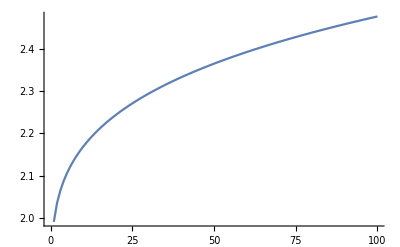

```mathematica
InvFitAcrossW=Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,0.1],{W,10,1000,10}];
ListLinePlot[InvFitAcrossW]
```

This is true if you increase the temperature (here increasing temperature from 270 to 310). Notice, however, that R_0 is lower for higher temperatures, indicating that increasing temperature negatively affects R_0.

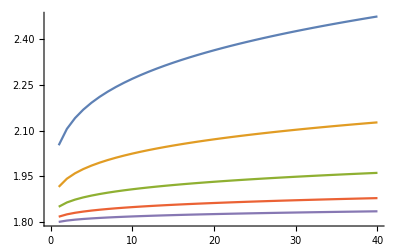

```mathematica
InvFitAcrossWT=Table[Table[NumSolInvFit[W,T,0.9,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{T,270,310,10}];
ListLinePlot[InvFitAcrossWT]
```

It also holds if you increase the cost of generalism (here decreasing c from 0.9 to 0.5):

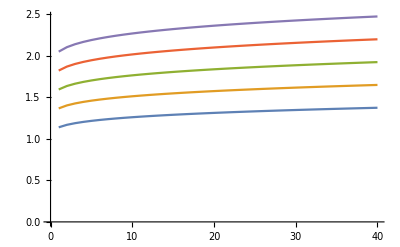

```mathematica
InvFitAcrossWc=Table[Table[NumSolInvFit[W,270,c,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{c,0.5,0.9,0.1}];ListLinePlot[InvFitAcrossWc]
```

It also holds if you reduce the size of the secondary host (here decreasing f from 0.9 to 0.5):

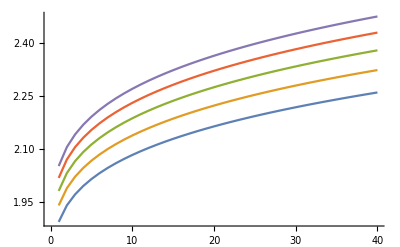

```mathematica
InvFitAcrossWf=Table[Table[NumSolInvFit[W,270,0.9,f,1,0.1,0.01,0.1],{W,25,1000,25}],{f,0.5,0.9,0.1}];
ListLinePlot[InvFitAcrossWf]
```

It also holds if you reduce the number of intermediate hosts (here N_T ranges from 0.25 to 2):

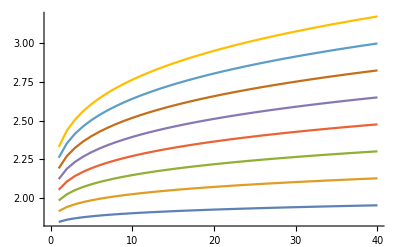

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.1,0.01,0.1],{W,25,1000,25}],{NT,0.25,2,0.25}];
ListLinePlot[InvFitAcrossWNT]
```

It also holds if you change the transmission rate to intermediate hosts (here β ranges from 0.05 to 0.55):

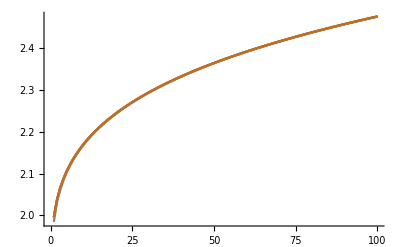

```mathematica
InvFitAcrossWB=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,B,0.01,0.1],{W,10,1000,10}],{B,0.05,0.55,0.1}];
ListLinePlot[InvFitAcrossWB]
```

It also holds if you change the rate parasites are lost from the environment (here γ ranges from 0.01 to 0.1):

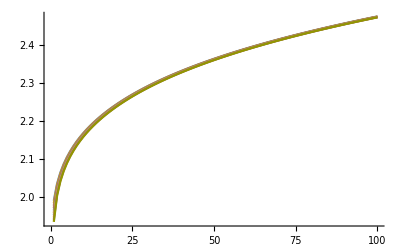

```mathematica
InvFitAcrossWg=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,g,0.1],{W,10,1000,10}],{g,0.01,0.1,0.01}];
ListLinePlot[InvFitAcrossWg]
```

It also holds if you change the ingestion rate of the definitive hosts:

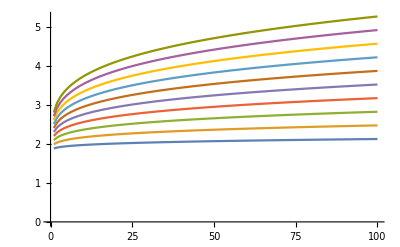

```mathematica
InvFitAcrossWa=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,a],{W,10,1000,10}],{a,0.05,0.5,0.05}];
ListLinePlot[InvFitAcrossWa]
```

Increasing temperature decreases R_0:

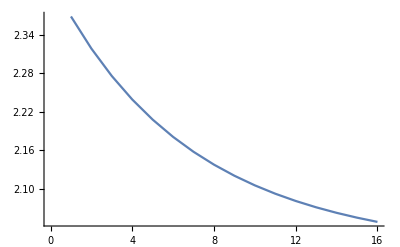

```mathematica
InvFitAcrossT=Table[NumSolInvFit[100,T,0.9,0.9,1],{T,270,300,2}];
ListLinePlot[InvFitAcrossT]
```

### Case 7: Trophic transmission; two specialist parasites; parasites regulate definitive host population sizes; active seeking of intermediate hosts; avoidance of infected intermediate hosts

Now we assume that there are two specialist parasites exploiting the same intermediate host, but infecting different definitive hosts. We let N_(2I r) track the number of intermediate hosts infected with the second specialist parasite and D_(2I r) track the number of secondary definitive hosts infected by the second specialist parasite.

```mathematica
dN1irdt=β (NT-N1ir-N2ir-Nim) P1r-a1(D1s+D1ir+D1im) N1ir-a2(D2s+D2ir+D2im) N1ir;
dN2irdt=β (NT-N1ir-N2ir-Nim) P2r-a1(D1s+D1ir+D1im)N2ir-a2 (D2s+D2ir+D2im) N2ir;
dNimdt=β (NT-N1ir-N2ir-Nim) Pm-a1(D1s+D1ir+D1im) Nim-a2 (D2s+D2ir+D2im) Nim;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+Nim);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+Nim);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dP1rdt=λ1 D1ir-β (NT-N1ir-N2ir-Nim) P1r-γ P1r;
dP2rdt=λ2 D2ir-β (NT-N1ir-N2ir-Nim) P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-N1ir-N2ir-Nim) Pm-γ Pm;
```

To determine whether the generalist can invade this system, we again look at the Jacobian.

```mathematica
J={{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r],
D[dN1irdt,N2ir],D[dN1irdt,D2s],D[dN1irdt,D2ir],D[dN1irdt,P2r],
D[dN1irdt,Nim],D[dN1irdt,D1im],D[dN1irdt,D2im],D[dN1irdt,Pm]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r],
D[dD1sdt,N2ir],D[dD1sdt,D2s],D[dD1sdt,D2ir],D[dD1sdt,P2r],
D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r],
D[dD1irdt,N2ir],D[dD1irdt,D2s],D[dD1irdt,D2ir],D[dD1irdt,P2r],
D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r],
D[dP1rdt,N2ir],D[dP1rdt,D2s],D[dP1rdt,D2ir],D[dP1rdt,P2r],
D[dP1rdt,Nim],D[dP1rdt,D1im],D[dP1rdt,D2im],D[dP1rdt,Pm]},
{D[dN2irdt,N1ir],D[dN2irdt,D1s],D[dN2irdt,D1ir],D[dN2irdt,P1r],
D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r],
D[dN2irdt,Nim],D[dN2irdt,D1im],D[dN2irdt,D2im],D[dN2irdt,Pm]},
{D[dD2sdt,N1ir],D[dD2sdt,D1s],D[dD2sdt,D1ir],D[dD2sdt,P1r],
D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r],
D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dD2irdt,N1ir],D[dD2irdt,D1s],D[dD2irdt,D1ir],D[dD2irdt,P1r],
D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r],
D[dD2irdt,Nim],D[dD2irdt,D1im],D[dD2irdt,D2im],D[dD2irdt,Pm]},
{D[dP2rdt,N1ir],D[dP2rdt,D1s],D[dP2rdt,D1ir],D[dP2rdt,P1r],
D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r],
D[dP2rdt,Nim],D[dP2rdt,D1im],D[dP2rdt,D2im],D[dP2rdt,Pm]},
{D[dNimdt,N1ir],D[dNimdt,D1s],D[dNimdt,D1ir],D[dNimdt,P1r],
D[dNimdt,N2ir],D[dNimdt,D2s],D[dNimdt,D2ir],D[dNimdt,P2r],
D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,N1ir],D[dD1imdt,D1s],D[dD1imdt,D1ir],D[dD1imdt,P1r],
D[dD1imdt,N2ir],D[dD1imdt,D2s],D[dD1imdt,D2ir],D[dD1imdt,P2r],
D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,N1ir],D[dD2imdt,D1s],D[dD2imdt,D1ir],D[dD2imdt,P1r],
D[dD2imdt,N2ir],D[dD2imdt,D2s],D[dD2imdt,D2ir],D[dD2imdt,P2r],
D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,N1ir],D[dPmdt,D1s],D[dPmdt,D1ir],D[dPmdt,P1r],
D[dPmdt,N2ir],D[dPmdt,D2s],D[dPmdt,D2ir],D[dPmdt,P2r],
D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}}/.{Nim->0,D1im->0,D2im->0,Pm->0};
```

As before, this matrix is upper block triangular. The upper left submatrix determines the stability of the system that doesn’t include the generalist parasite. It will be helpful to look at the eigenvalues of this submatrix at the parasite-free equilibrium when both specialist parasites are absent (N_(1I r)=0, N_(2I r)=0, D_(1S)=K_1, D_(1 I r)=0, D_(2 S)=K_2, D_(2 I r)=0, P_1=0, P_2=0)? In particular, we want all of these eigenvalues to be positive to guarantee that the specialist parasites can both persist in the system. Notice that this matrix is block diagonal, so we can simply look at the eigenvalues of each submatrix to determine the eigenvalues of the full matrix.

```mathematica
J[[1;;8,1;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0}//MatrixForm
```

(-a1 K1-a2 K2 | 0 | 0 | NT β | 0 | 0 | 0 | 0
-a1 K1 | -r1 | -r1 | 0 | 0 | 0 | 0 | 0
a1 K1 | 0 | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ1 | -NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a1 K1-a2 K2 | 0 | 0 | NT β
0 | 0 | 0 | 0 | -a2 K2 | -r2 | -r2 | 0
0 | 0 | 0 | 0 | a2 K2 | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ2 | -NT β-γ)

Applying the next generation matrix, we find that for the specialist-absent system to be unstable, we require that
(β N_T)/(β N_T+γ) ((a_1 K_1)/(a_1 K_1+a_2 K_2)λ_1/μ_1)>1 and (β N_T)/(β N_T+γ) ((a_2 K_2)/(a_1 K_1+a_2 K_2)λ_2/μ_2)>1

```mathematica
F1={{0,0,0,NT β},{0,0,0,0},{a1 K1,0,0,0},{0,0,λ1,0}};
V1={{a1 K1+a2 K2,0,0,0},{a1 K1,r1,r1,0},{0,0,μ1,0},{0,0,0,NT β+γ}};
(J[[1;;4,1;;4]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F1-V1
Eigenvalues[Dot[F1,Inverse[V1]]]
(Eigenvalues[Dot[F1,Inverse[V1]]][[2]])^3==(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)
F2={{0,0,0,NT β},{0,0,0,0},{a2 K2,0,0,0},{0,0,λ2,0}};
V2={{a1 K1+a2 K2,0,0,0},{a2 K2,r2,r2,0},{0,0,μ2,0},{0,0,0,NT β+γ}};
(J[[5;;8,5;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F2-V2
Eigenvalues[Dot[F2,Inverse[V2]]]
(Eigenvalues[Dot[F2,Inverse[V2]]][[2]])^3==(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)
```

True

{0,(a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3))}

True

True

{0,(a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3))}

True

We assume that both of those inequalities are satisfied. Whether the generalist can invade the system depends on the eigenvalues of the lower right submatrix of J:

```mathematica
MatrixForm[J[[9;;12,9;;12]]]
```

(-a1 (D1ir+D1s)-a2 (D2ir+D2s) | 0 | 0 | (-N1ir-N2ir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-N1ir-N2ir+NT) β-γ)

Using the next generation matrix theorem, the Jacobian will have a positive eigenvalue whenever the second value is greater than 1.

```mathematica
F={{0,0,0,(NT-N1ir-N2ir) β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1,c λ2,0}};
V={{a1 (D1ir+D1s)+a2(D2ir+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,(NT-N1ir-N2ir) β+γ}};
J[[9;;12,9;;12]]==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

This eigenvalue is equivalent to the expression given below:

```mathematica
((c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)))^3==((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) ((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)//Simplify
```

True

As before, it is impossible to make headway analytically, so we must resort to numerical solutions.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
(*Print[(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)/.allom/.pars];*)
(*Print[(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)/.allom/.pars];*)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1ir'[t]==β (NT-N1ir[t]-N2ir[t]) P1r[t]-a1(D1s[t]+D1ir[t]) N1ir[t]-a2(D2s[t]+D2ir[t]) N1ir[t],
N2ir'[t]==β (NT-N1ir[t]-N2ir[t]) P2r[t]-a1(D1s[t]+D1ir[t]) N2ir[t]-a2(D2s[t]+D2ir[t]) N2ir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] N1ir[t],
D2s'[t]==r2 (D2s[t]+D2ir[t]) (1-(D2s[t]+D2ir[t])/K2)-a2 D2s[t] N2ir[t],
D1ir'[t]==a1 D1s[t] N1ir[t]-μ1 D1ir[t],
D2ir'[t]==a2 D2s[t] N2ir[t]-μ1 D2ir[t],
P1r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P1r[t]-γ P1r[t],
P2r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P2r[t]-γ P2r[t],
N1ir[0]==0,N2ir[0]==0,
D1s[0]==0.1,D2s[0]==0.1,
D1ir[0]==0,D2ir[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1ir,N2ir,D1s,D1ir,D2s,D2ir,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) ((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)/.{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}/.allom/.pars
];
```

One case is sufficient to demonstrate that the response of the generalist’s R_0 to changes in host body size is much more complex here. Consider the effect of changing the definitive host body sizes across a gradient of intermediate host abundance. You can see very clearly that the responses depend on the value of N_T: when N_T is small, increasing host mass increases R_0; when N_T is large, increasing host mass first increases, then decreases R_0. 

In reality, the abundance of the definitive host’s prey is likely to be related to the size of the definitive host: in general, larger-bodied hosts are more likely to consume larger-bodied prey, whose carrying capacities would decrease commensurately. That is, as definitive host body size goes up, you would expect intermediate host carrying capacity to go down.

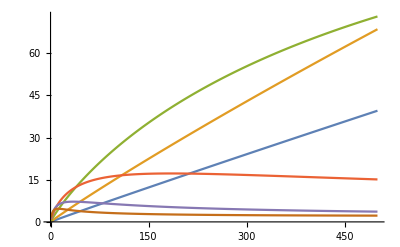

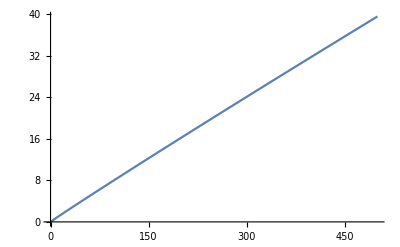

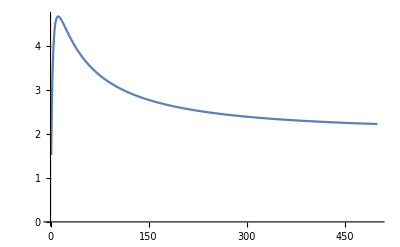

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,10,5000,10}],{NT,{0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[InvFitAcrossWNT]
ListLinePlot[InvFitAcrossWNT[[1]]]
ListLinePlot[InvFitAcrossWNT[[6]]]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

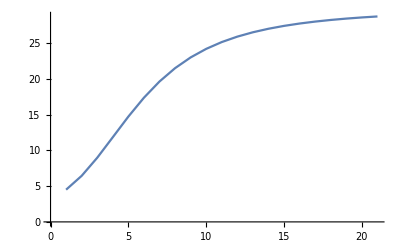

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

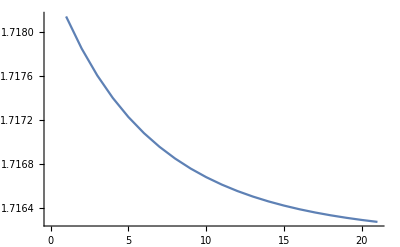

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

### Case 8: Trophic transmission; two specialist parasites; constant definitive host population sizes; active seeking of intermediate hosts; avoidance of infected intermediate hosts

We assume that both the intermediate and definitive hosts have constant population size. Let K_N be the total number of intermediate hosts; let N_(1,r) be the number of intermediate hosts infected by the first specialist parasite; let N_(2,r) be the number of intermediate hosts infected by the second specialist parasite, and let N_(12,m) be the fraction of intermediate hosts infected by the generalist parasite. Then K_N-N_(1,r)-N_(2,r) is the number of susceptible intermediate hosts - we assume that each intermediate host can only be infected by a single parasite. Let K_1 be the abundance of the first definitive host population and let K_2 be the abundance of the second definitive host population. Let I_(1,r) and I_(2,r) be the numbers of the first and second definitive host populations, respectively, that are infected by the specialist parasites, and let I_(1,m) and I_(2,m) be the numbers of the definitive host populations infected by the generalist parasite. Let P_(1,r) and P_(2,r) be the numbers of the two specialist parasites in the environment and let P_(12,m) be the number of generalist parasites in the environment.

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-a N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-a N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-a N12m (K1+K2);

dI1rdt=a(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=a(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=a(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=a(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r (KN-N1r-N2r-N12m)-γ P1r;
dP2rdt=λ2 I2r-β P2r (KN-N1r-N2r-N12m)-γ P2r;
dP12mdt=c λ1 I1m+c λ2 I2m-β P12m (KN-N1r-N2r-N12m)-γ P12m;
```

The Jacobian is needed to inform us about the stability of the system.

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}};
```

Before we can investigate whether the generalist can invade or not, we need to establish the conditions necessary for the specialist parasites to be able to persist in the system. That is, we are interested in the stability of the equilibrium where N_(1r), N_(2r),I_(1r), I_(2r), P_(1r) and P_(2r) are all equal to 0.

```mathematica
J[[1;;6,1;;6]]/.{N1r->0,N2r->0,I1r->0,I2r->0,P1r->0,P2r->0,N12m->0,I1m->0,I2m->0,P12m->0}//MatrixForm
```

(-a (K1+K2) | 0 | 0 | 0 | KN β | 0
0 | -a (K1+K2) | 0 | 0 | 0 | KN β
a K1 | 0 | -μ1 | 0 | 0 | 0
0 | a K2 | 0 | -μ2 | 0 | 0
0 | 0 | λ1 | 0 | -KN β-γ | 0
0 | 0 | 0 | λ2 | 0 | -KN β-γ)

Applying the next generation matrix theorem:

```mathematica
F={{0,0,0,0,KN β,0},{0,0,0,0,0,KN β},{a K1,0,0,0,0,0},{0,a K2,0,0,0,0},{0,0,λ1,0,0,0},{0,0,0,λ2,0,0}};
V={{a (K1+K2),0,0,0,0,0},{0,a (K1+K2),0,0,0,0},{0,0,μ1,0,0,0},{0,0,0,μ2,0,0},{0,0,0,0,KN β+γ,0},{0,0,0,0,0,KN β+γ}};
(J[[1;;6,1;;6]]/.{N1r->0,N2r->0,I1r->0,I2r->0,P1r->0,P2r->0,N12m->0,I1m->0,I2m->0,P12m->0})==F-V
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{(K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),(K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3))}

This equilibrium will be unstable, allowing both specialists to persist, as long as both (K1 KN β λ1)/((K1+K2) (KN β+γ) μ1) > 0 and (K2 KN β λ2)/((K1+K2) (KN β+γ) μ2)> 0.

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{N12m->0,I1m->0,I2m->0,P12m->0}]
```

(-a (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
a (-I1r+K1) | -μ1 | 0 | 0
a (-I2r+K2) | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(KN-N1r-N2r) β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{a S1,0,0,0},{a S2,0,0,0},{0,c λ1, c λ2,0}};
V={{a(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β Ns+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-a (K1+K2) | 0 | 0 | Ns β
a S1 | -μ1 | 0 | 0
a S2 | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns β-γ)

{0,(c^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(c β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β N_S+γ) μ_1 μ_2)>1
c λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β N_S+γ) (c λ_2 μ_1 S_2+c λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β N_S+γ) (S_1/(K_1+K_2)(c λ_1)/μ_1 +S_2/(K_1+K_2)(c λ_2)/μ_2 )>1

where
(β N_s)/(β N_S+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(c λ_1)/μ_1 and (c λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β Ns+γ) (S1/(K1+K2) (c λ1)/μ1+S2/(K1+K2) (c λ2)/μ2);
```

To find the generalist-free equilibrium, we first make use of the fact that (dP_(1r))/dt=0 implies that β P_(1r)(K_N-N_(1r)-N_(2r))=λ_1 I_(1r)-γ P_(1r) and that (dP_(2r))/dt=0 implies that β P_(2r)(K_N-N_(1r)-N_(2r))=λ_2 I_(2r)-γ P_(2r).

```mathematica
I1rEq=Solve[λ1 I1r-γ P1r-c N1r (K1+K2)==0,I1r][[1,1,2]]
I2rEq=Solve[λ2 I2r-γ P2r-c N2r (K1+K2)==0,I2r][[1,1,2]]
```

(c K1 N1r+c K2 N1r+P1r γ)/λ1

(c K1 N2r+c K2 N2r+P2r γ)/λ2

```mathematica
P1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,P1r][[1,1,2]]
P2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,P2r][[1,1,2]]
```

(-a c K1 N1r^2-a c K2 N1r^2+a K1 N1r λ1-c K1 N1r μ1-c K2 N1r μ1)/(γ (a N1r+μ1))

(-a c K1 N2r^2-a c K2 N2r^2+a K2 N2r λ2-c K1 N2r μ2-c K2 N2r μ2)/(γ (a N2r+μ2))

```mathematica
I1rEq=I1rEq/.P1r->P1rEq//Simplify
I2rEq=I2rEq/.P2r->P2rEq//Simplify
```

(a K1 N1r)/(a N1r+μ1)

(a K2 N2r)/(a N2r+μ2)

```mathematica
N1rEq=Solve[(dP1rdt/.I1r->I1rEq/.P1r->P1rEq/.{N12m->0})==0,N1r]
```

{{N1r→0},{N1r→1/(2 (-a c K1 β-a c K2 β))(-a c K1 KN β-a c K2 KN β+a c K1 N2r β+a c K2 N2r β-a c K1 γ-a c K2 γ-a K1 β λ1+c K1 β μ1+c K2 β μ1-√((a c K1 KN β+a c K2 KN β-a c K1 N2r β-a c K2 N2r β+a c K1 γ+a c K2 γ+a K1 β λ1-c K1 β μ1-c K2 β μ1)^2-4 (-a c K1 β-a c K2 β) (-a K1 KN β λ1+a K1 N2r β λ1+c K1 KN β μ1+c K2 KN β μ1-c K1 N2r β μ1-c K2 N2r β μ1+c K1 γ μ1+c K2 γ μ1)))},{N1r→1/(2 (-a c K1 β-a c K2 β))(-a c K1 KN β-a c K2 KN β+a c K1 N2r β+a c K2 N2r β-a c K1 γ-a c K2 γ-a K1 β λ1+c K1 β μ1+c K2 β μ1+√((a c K1 KN β+a c K2 KN β-a c K1 N2r β-a c K2 N2r β+a c K1 γ+a c K2 γ+a K1 β λ1-c K1 β μ1-c K2 β μ1)^2-4 (-a c K1 β-a c K2 β) (-a K1 KN β λ1+a K1 N2r β λ1+c K1 KN β μ1+c K2 KN β μ1-c K1 N2r β μ1-c K2 N2r β μ1+c K1 γ μ1+c K2 γ μ1)))}}

```mathematica
N2rEq=Solve[(dP2rdt/.I2r->I2rEq/.P2r->P2rEq/.{N12m->0}/.N1r->N1rEq[[3,1,2]])==0,N2r]
```

{{N2r→0},{N2r→1/(2 (c^2 K1 β λ1+c^2 K2 β λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√((-c^2 K2 KN β λ2-c^2 K2 γ λ2-c K1 β λ1 λ2+(c K1^2 β λ1 λ2)/(K1+K2)+c K1 β λ2^2-c K2 β λ2^2-(c K1^2 β λ2^2)/(K1+K2)-c K2 β λ2 μ1+2 c K1 β λ1 μ2+c K2 β λ2 μ2)^2-4 (c^2 K1 β λ1+c^2 K2 β λ2) (-c K1 KN β λ2^2+c K2 KN β λ2^2+(c K1^2 KN β λ2^2)/(K1+K2)-K1 β λ2^2 μ1+K2 β λ2^2 μ1+(K1^2 β λ2^2 μ1)/(K1+K2)-c K2 KN β λ2 μ2-c K2 γ λ2 μ2-K1 β λ1 λ2 μ2+(K1^2 β λ1 λ2 μ2)/(K1+K2)-K2 β λ2 μ1 μ2+K1 β λ1 μ2^2)))},{N2r→1/(2 (c^2 K1 β λ1+c^2 K2 β λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2+√((-c^2 K2 KN β λ2-c^2 K2 γ λ2-c K1 β λ1 λ2+(c K1^2 β λ1 λ2)/(K1+K2)+c K1 β λ2^2-c K2 β λ2^2-(c K1^2 β λ2^2)/(K1+K2)-c K2 β λ2 μ1+2 c K1 β λ1 μ2+c K2 β λ2 μ2)^2-4 (c^2 K1 β λ1+c^2 K2 β λ2) (-c K1 KN β λ2^2+c K2 KN β λ2^2+(c K1^2 KN β λ2^2)/(K1+K2)-K1 β λ2^2 μ1+K2 β λ2^2 μ1+(K1^2 β λ2^2 μ1)/(K1+K2)-c K2 KN β λ2 μ2-c K2 γ λ2 μ2-K1 β λ1 λ2 μ2+(K1^2 β λ1 λ2 μ2)/(K1+K2)-K2 β λ2 μ1 μ2+K1 β λ1 μ2^2)))}}

Based on the complexity of these two expression, we are unlikely to be able to make any headway analytically.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1r'[t]==-a (K1+K2) N1r[t]+β (NT-N1r[t]-N2r[t]) P1r[t],
N2r'[t]==-a (K1+K2) N2r[t]+β (NT-N1r[t]-N2r[t]) P2r[t],
I1r'[t]==-μ1 I1r[t]+a (K1-I1r[t]) N1r[t],
I2r'[t]==-μ2 I2r[t]+a (K2-I2r[t]) N2r[t],
P1r'[t]==λ1 I1r[t]-γ P1r[t]-β (NT-N1r[t]-N2r[t]) P1r[t],
P2r'[t]==λ2 I2r[t]-γ P2r[t]-β (NT-N1r[t]-N2r[t]) P2r[t],
N1r[0]==0,N2r[0]==0,
I1r[0]==0,I2r[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1r,N2r,I1r,I2r,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
(β (NT-N1r-N2r))/(β (NT-N1r-N2r)+γ) ((K1-I1r)/(K1+K2) (c λ1)/μ1+(K2-I2r)/(K1+K2) (c λ2)/μ2)/.{N1r->(N1r[1000]/.Soln)[[1]],N2r->(N2r[1000]/.Soln)[[1]],I1r->(I1r[1000]/.Soln)[[1]],I2r->(I2r[1000]/.Soln)[[1]]}/.allom/.pars
];
```

As with the preceding model, there is not a simple relationship between R_0 and mass. For example, when intermediate host abundance is small, increasing mass increases R_0, but when intermediate host abundance is high, increasing host mass first increases, and then decreases, R_0.

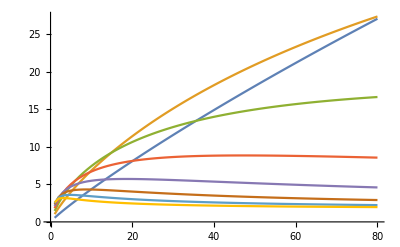

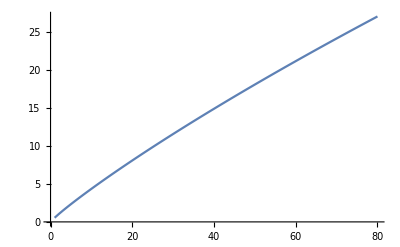

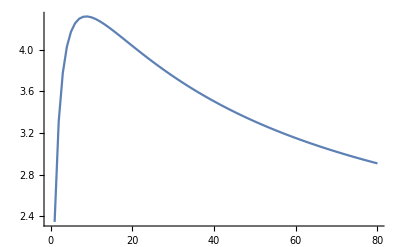

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,25,2000,25}],{NT,0.25,2,0.25}];
ListLinePlot[InvFitAcrossWNT]
ListLinePlot[InvFitAcrossWNT[[1]]]
ListLinePlot[InvFitAcrossWNT[[6]]]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

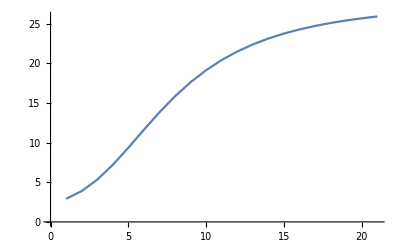

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

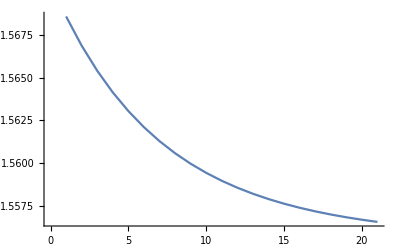

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

It also holds if you change the rate parasites are lost from the environment (here γ ranges from 0.01 to 0.1):

```mathematica
InvFitAcrossWg=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,g,0.1],{W,10,1000,10}],{g,0.01,0.1,0.01}];
ListLinePlot[InvFitAcrossWg]
```

-Graphics-

It also holds if you change the ingestion rate of the definitive hosts:

```mathematica
InvFitAcrossWa=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,a],{W,10,1000,10}],{a,0.05,0.5,0.05}];
ListLinePlot[InvFitAcrossWa]
```

-Graphics-

Increasing temperature decreases R_0:

```mathematica
InvFitAcrossT=Table[NumSolInvFit[100,T,0.9,0.9,1],{T,270,300,2}];
ListLinePlot[InvFitAcrossT]
```

-Graphics-

### Case 9: Trophic transmission; two specialist parasites; constant host population size; active seeking of intermediate hosts; no avoidance of infected intermediate hosts

We have assumed that parasites in the environment are consumed by all intermediate hosts, even though they only cause new infections in susceptible intermediate hosts. This makes the problem very analytically tractable.

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-c N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-c N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-c N12m (K1+K2);

dI1rdt=c(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=c(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=c(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=c(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r KN-γ P1r;
dP2rdt=λ2 I2r-β P2r KN-γ P2r;
dP12mdt=a λ1 I1m+a λ2 I2m-β P12m KN-γ P12m;
```

Find the equilibria (the brute force, all at once technique failed for this model):

```mathematica
I1rEq=Solve[dP1rdt==0,I1r][[1,1,2]]
I2rEq=Solve[dP2rdt==0,I2r][[1,1,2]]
```

(KN P1r β+P1r γ)/λ1

(KN P2r β+P2r γ)/λ2

```mathematica
N1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,N1r][[1,1,2]]
N2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,N2r][[1,1,2]]
```

-((KN P1r β+P1r γ) μ1)/(c (KN P1r β+P1r γ-K1 λ1))

-((KN P2r β+P2r γ) μ2)/(c (KN P2r β+P2r γ-K2 λ2))

```mathematica
P1rEq=Simplify[Solve[(dN1rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0})==0,P1r]][[2,1,2]]
P2rEq=Simplify[Solve[(dN2rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0}/.{P1r->P1rEq})==0,P2r]][[2,1,2]]
```

(-c (KN P2r β+P2r γ-K2 λ2) (K2 (KN β+γ) μ1+K1 (γ μ1+KN β (-λ1+μ1)))+K1 P2r β (KN β+γ) λ1 μ2)/(β (KN β+γ) (c KN (KN P2r β+P2r γ-K2 λ2)+P2r γ μ1-K2 λ2 μ1+P2r γ μ2+KN P2r β (μ1+μ2)))

(β (K2 λ2 μ1-K1 λ1 μ2)-c (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))/(β (KN β+γ) (c KN+μ1+μ2))

The number of susceptible intermediate hosts at the generalist-free equilibrium is N_S=K_N-N_(1,r)-N_(2,r):

```mathematica
NsEq=Simplify[KN-Simplify[Simplify[N1rEq/.P1r->P1rEq/.P2r->P2rEq]+Simplify[N2rEq/.P2r->P2rEq]]]
```

((K1+K2) (KN β+γ) (c KN+μ1+μ2))/(c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2))

The number of susceptible definitive hosts of species 1 and 2 at the generalist free-equilibrium are S_1=K_1-I_(1,r) and S_2=K_2-I_(2,r), respectively:

```mathematica
S1Eq=Simplify[(K1-I1r)/.I1r->I1rEq/.P1r->P1rEq/.P2r->P2rEq]
S2Eq=Simplify[(K2-I2r)/.I2r->I2rEq/.P2r->P2rEq]
```

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ1)/(β λ1 (c KN+μ1+μ2))

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ2)/(β λ2 (c KN+μ1+μ2))

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{N12m->0,I1m->0,I2m->0,P12m->0};
```

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]]
```

(-c (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
c (-I1r+K1) | -μ1 | 0 | 0
c (-I2r+K2) | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{c S1,0,0,0},{c S2,0,0,0},{0,a λ1, a λ2,0}};
V={{c(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β KN+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-c (K1+K2) | 0 | 0 | Ns β
c S1 | -μ1 | 0 | 0
c S2 | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

{0,(a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(a β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β K_N+γ) μ_1 μ_2)>1
a λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β K_N+γ) (a λ_2 μ_1 S_2+a λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β K_N+γ) (S_1/(K_1+K_2)(a λ_1)/μ_1 +S_2/(K_1+K_2)(a λ_2)/μ_2 )>1

where
(β N_s)/(β K_N+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(a λ_1)/μ_1 and (a λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β KN+γ) (S1/(K1+K2) (a λ1)/μ1+S2/(K1+K2) (a λ2)/μ2);
```

If you plug in the equilibrium values of N_S,S_1 and S_2, however, you get an incredibly simple expression for the invasion fitness:

```mathematica
Simplify[R0/.{Ns->NsEq,S1->S1Eq,S2->S2Eq}]
```

2 a

What this indicates is that as long as the fraction that shedding is reduced for the generalist (the cost of generalism) is less than 0.5, the generalist will be able to invade.

### Case 10: Trophic transmission; two specialist parasites; constant host population size; passive host seeking; no avoidance of infected intermediate hosts

For this model, we have assumed that parasites in the environment are consumed by all hosts (both definitive and intermediate), even though they only cause new infections in susceptible intermediate hosts.

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-c N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-c N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-c N12m (K1+K2);

dI1rdt=c(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=c(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=c(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=c(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r (KN+K1+K2)-γ P1r;
dP2rdt=λ2 I2r-β P2r (KN+K1+K2)-γ P2r;
dP12mdt=a λ1 I1m+a λ2 I2m-β P12m (KN+K1+K2)-γ P12m;
```

Find the equilibria (the brute force, all at once technique failed for this model):

```mathematica
I1rEq=Solve[dP1rdt==0,I1r][[1,1,2]]
I2rEq=Solve[dP2rdt==0,I2r][[1,1,2]]
```

(K1 P1r β+K2 P1r β+KN P1r β+P1r γ)/λ1

(K1 P2r β+K2 P2r β+KN P2r β+P2r γ)/λ2

```mathematica
N1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,N1r][[1,1,2]]
N2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,N2r][[1,1,2]]
```

-((K1 P1r β+K2 P1r β+KN P1r β+P1r γ) μ1)/(c (K1 P1r β+K2 P1r β+KN P1r β+P1r γ-K1 λ1))

-((K1 P2r β+K2 P2r β+KN P2r β+P2r γ) μ2)/(c (K1 P2r β+K2 P2r β+KN P2r β+P2r γ-K2 λ2))

```mathematica
P1rEq=Simplify[Solve[(dN1rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0})==0,P1r]][[2,1,2]]
P2rEq=Simplify[Solve[(dN2rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0}/.{P1r->P1rEq})==0,P2r]][[2,1,2]]
```

(-c (K1 P2r β+K2 P2r β+KN P2r β+P2r γ-K2 λ2) (K1^2 β μ1+K2 (K2 β+KN β+γ) μ1+K1 ((2 K2 β+γ) μ1+KN β (-λ1+μ1)))+K1 P2r β (K1 β+K2 β+KN β+γ) λ1 μ2)/(β (K1 β+K2 β+KN β+γ) (c KN (K1 P2r β+K2 P2r β+KN P2r β+P2r γ-K2 λ2)+K2 P2r β μ1+KN P2r β μ1+P2r γ μ1-K2 λ2 μ1+K2 P2r β μ2+KN P2r β μ2+P2r γ μ2+K1 P2r β (μ1+μ2)))

(β (K2 λ2 μ1-K1 λ1 μ2)-c (K2^2 β μ2+K1 (K1 β+KN β+γ) μ2+K2 ((2 K1 β+γ) μ2+KN β (-λ2+μ2))))/(β (K1 β+K2 β+KN β+γ) (c KN+μ1+μ2))

The number of susceptible intermediate hosts at the generalist-free equilibrium is N_S=K_N-N_(1,r)-N_(2,r):

```mathematica
NsEq=Simplify[KN-Simplify[Simplify[N1rEq/.P1r->P1rEq/.P2r->P2rEq]+Simplify[N2rEq/.P2r->P2rEq]]]
```

((K1+K2) (K1 β+K2 β+KN β+γ) (c KN+μ1+μ2))/(c (K1+K2) (K1 β+K2 β+KN β+γ)+β (K1 λ1+K2 λ2))

The number of susceptible definitive hosts of species 1 and 2 at the generalist free-equilibrium are S_1=K_1-I_(1,r) and S_2=K_2-I_(2,r), respectively:

```mathematica
S1Eq=Simplify[(K1-I1r)/.I1r->I1rEq/.P1r->P1rEq/.P2r->P2rEq]
S2Eq=Simplify[(K2-I2r)/.I2r->I2rEq/.P2r->P2rEq]
```

((c (K1+K2) (K1 β+K2 β+KN β+γ)+β (K1 λ1+K2 λ2)) μ1)/(β λ1 (c KN+μ1+μ2))

((c (K1+K2) (K1 β+K2 β+KN β+γ)+β (K1 λ1+K2 λ2)) μ2)/(β λ2 (c KN+μ1+μ2))

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{N12m->0,I1m->0,I2m->0,P12m->0};
```

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]]
```

(-c (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
c (-I1r+K1) | -μ1 | 0 | 0
c (-I2r+K2) | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -(K1+K2+KN) β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{c S1,0,0,0},{c S2,0,0,0},{0,a λ1, a λ2,0}};
V={{c(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β (KN+K1+K2)+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-c (K1+K2) | 0 | 0 | Ns β
c S1 | -μ1 | 0 | 0
c S2 | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -(K1+K2+KN) β-γ)

{0,(a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (K1 β+K2 β+KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (K1 β+K2 β+KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (K1 β+K2 β+KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(β N_s)/(β (K_N+K_1+K_2)+γ) (S_1/(K_1+K_2)(a λ_1)/μ_1 +S_2/(K_1+K_2)(a λ_2)/μ_2 )>1

where
(β N_s)/(β (K_N+K_1+K_2)+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(a λ_1)/μ_1 and (a λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β (KN+K1+K2)+γ) (S1/(K1+K2) (a λ1)/μ1+S2/(K1+K2) (a λ2)/μ2);
```

If you plug in the equilibrium values of N_S,S_1 and S_2, however, you get an incredibly simple expression for the invasion fitness:

```mathematica
Simplify[R0/.{Ns->NsEq,S1->S1Eq,S2->S2Eq}]
```

2 a

What this indicates is that as long as the fraction that shedding is reduced for the generalist (the cost of generalism) is less than 0.5, the generalist will be able to invade.

### Specialist invading generalist

```mathematica
dI1rdt=β (K1-I1r-I1m) Pr-μ1 I1r;
dI2rdt=β (K2-I2r) Pr-μ2 I2r;
dPrdt=λ1 I1r+λ2 I2r-β (K1-I1r-I1m+K2-I2r) Pr-γ Pr;
dI1mdt=β (K1-I1r-I1m) Pm-μ1 I1m;
dPmdt=a λ1 I1m-β (K1-I1r-I1m) Pm-γ Pm;
```

To determine the stability of any possible equilibria, we need to calculate the Jacobian matrix of partial derivatives.

```mathematica
J={{D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,Pr],D[dI1rdt,I1m],D[dI1rdt,Pm]},
{D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,Pr],D[dI2rdt,I1m],D[dI2rdt,Pm]},
{D[dPrdt,I1r],D[dPrdt,I2r],D[dPrdt,Pr],D[dPrdt,I1m],D[dPrdt,Pm]},
{D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,Pr],D[dI1mdt,I1m],D[dI1mdt,Pm]},
{D[dPmdt,I1r],D[dPmdt,I2r],D[dPmdt,Pr],D[dPmdt,I1m],D[dPmdt,Pm]}};
MatrixForm[J]
```

(-Pr β-μ1 | 0 | (-I1m-I1r+K1) β | -Pr β | 0
0 | -Pr β-μ2 | (-I2r+K2) β | 0 | 0
Pr β+λ1 | Pr β+λ2 | -(-I1m-I1r-I2r+K1+K2) β-γ | Pr β | 0
-Pm β | 0 | 0 | -Pm β-μ1 | (-I1m-I1r+K1) β
Pm β | 0 | 0 | Pm β+a λ1 | -(-I1m-I1r+K1) β-γ)

The submatrix contained in the first three rows and columns is informative of the stability of the specialist-free system (I_(1m)=0, P_m=0). An important equilibrium for this system is the generalist-free equilibrium - we need this equilibrium to be unstable. Applying the next generation matrix theorem we have that this equilibrium is unstable if (β (K2 λ2 μ1+K1 λ1 μ2))/((K1 β+K2 β+γ) μ1 μ2)>1. This is equivalent to requiring that K2 β μ1 (λ2-μ2)+K1 β (λ1-μ1) μ2-γ μ1 μ2 > 0

```mathematica
J[[1;;3,1;;3]]/.{Pr->0,I1r->0,I1m->0,I2r->0,Pm->0}//MatrixForm
F={{0,0,β K1},{0,0,β K2},{λ1, λ2, 0}};
V={{μ1,0,0},{0,μ2,0},{0,0,β (K1+K2)+γ}};
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[3]])^2
```

(-μ1 | 0 | K1 β
0 | -μ2 | K2 β
λ1 | λ2 | -(K1+K2) β-γ)

{0,-(√β √(K2 λ2 μ1+K1 λ1 μ2))/(√(K1 β+K2 β+γ) √μ1 √μ2),(√β √(K2 λ2 μ1+K1 λ1 μ2))/(√(K1 β+K2 β+γ) √μ1 √μ2)}

(β (K2 λ2 μ1+K1 λ1 μ2))/((K1 β+K2 β+γ) μ1 μ2)

```mathematica
β (K2 λ2 μ1+K1 λ1 μ2)-(K1 β+K2 β+γ) μ1 μ2==K2 β μ1 (λ2-μ2)+K1 β μ2 (λ1-μ1)-γ μ1 μ2//Simplify
```

True

To determine when

```mathematica
J[[4;;5,4;;5]]
F={{0,(-I1r+K1) β},{a λ1,0}};
V={{μ1,0},{0,(-I1r+K1) β+γ}};
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^2
```

{{-Pm β-μ1,(-I1m-I1r+K1) β},{Pm β+a λ1,-(-I1m-I1r+K1) β-γ}}

{-(√a √(I1r-K1) √β √λ1)/(√(I1r β-K1 β-γ) √μ1),(√a √(I1r-K1) √β √λ1)/(√(I1r β-K1 β-γ) √μ1)}

(a (I1r-K1) β λ1)/((I1r β-K1 β-γ) μ1)

The only equilibrium we need be concerned with is I_(1r):

```mathematica
Eq=Solve[({dI1rdt==0,dI2rdt==0,dPrdt==0}/.{I1m->0,Pm->0}),{I1r,I2r,Pr}];Simplify[Eq[[1;;3,1]]]
```

{I1r→0,I1r→-1/(4 β^3 γ (λ1-μ1) (μ1-μ2))(K1 β^2 λ1+K2 β^2 λ2-K1 β^2 μ1+β γ μ1-K2 β^2 μ2-β γ μ2+√(β^2 (-4 γ ((γ μ1+K1 β (-λ1+μ1)) μ2+K2 β μ1 (-λ2+μ2))+(K1 β (-λ1+μ1)+K2 β (-λ2+μ2)+γ (μ1+μ2))^2))) (-K1 β^2 λ1-K2 β^2 λ2+K1 β^2 μ1+β γ μ1+K2 β^2 μ2+β γ μ2+√(β^2 (-4 γ ((γ μ1+K1 β (-λ1+μ1)) μ2+K2 β μ1 (-λ2+μ2))+(K1 β (-λ1+μ1)+K2 β (-λ2+μ2)+γ (μ1+μ2))^2))),I1r→-1/(4 β^3 γ (λ1-μ1) (μ1-μ2))(K1 β^2 λ1+K2 β^2 λ2-K1 β^2 μ1-β γ μ1-K2 β^2 μ2-β γ μ2+√(β^2 (-4 γ ((γ μ1+K1 β (-λ1+μ1)) μ2+K2 β μ1 (-λ2+μ2))+(K1 β (-λ1+μ1)+K2 β (-λ2+μ2)+γ (μ1+μ2))^2))) (-K1 β^2 λ1-K2 β^2 λ2+K1 β^2 μ1-β γ μ1+K2 β^2 μ2+β γ μ2+√(β^2 (-4 γ ((γ μ1+K1 β (-λ1+μ1)) μ2+K2 β μ1 (-λ2+μ2))+(K1 β (-λ1+μ1)+K2 β (-λ2+μ2)+γ (μ1+μ2))^2)))}

Looking at that second equilibrium, it can be rewritten as:

```mathematica
Assuming[β>0&&γ>0&&μ1>0,Simplify[Eq⟦2,1,2⟧==1/(4 β^3 γ (λ1-μ1) (μ1-μ2))(2 β^2 γ (-K2 β μ1 (λ2-μ2)-K1 β μ2 (λ1-μ1)+γ μ1 μ2-K1 β (λ1-μ1) (μ2-μ1)-γ μ1^2)-Sqrt[(2 β^2 γ (-K2 β μ1 (λ2-μ2)-K1 β μ2 (λ1-μ1)+γ μ1 μ2-K1 β (λ1-μ1) (μ2-μ1)-γ μ1^2))^2+16 K1 β^5 γ^2 (λ1-μ1) (μ1-μ2) (K2 β μ1 (λ2-μ2)+(K1 β (λ1-μ1)-γ μ1) μ2)])]]
```

True

Notice that -K2 β μ1 (λ2-μ2)-K1 β μ2 (λ1-μ1)+γ μ1 μ2-K1 β (λ1-μ1) (μ2-μ1)-γ μ1^2 must be negative, as K2 β μ1 (λ2-μ2)+K1 β μ2 (λ1-μ1)-γ μ1 μ2>0 is the condition for the generalist parasite to be able to persist in the system and μ_2>μ_1 by the assumption that host 2 is smaller than host 1.

```mathematica
Simplify[2 K1 β^3 γ λ1 μ1-2 K2 β^3 γ λ2 μ1-2 K1 β^3 γ μ1^2-2 β^2 γ^2 μ1^2-4 K1 β^3 γ λ1 μ2+4 K1 β^3 γ μ1 μ2+2 K2 β^3 γ μ1 μ2+2 β^2 γ^2 μ1 μ2==2 β^2 γ (-K2 β μ1 (λ2-μ2)-K1 β μ2 (λ1-μ1)+γ μ1 μ2-K1 β (λ1-μ1) (μ2-μ1)-γ μ1^2)]
```

True

That means that this entire equilibrium must be negative, because we have a negative number and we are subtracting a number which larger in magnitude than it. Thus, since equilibrium 2 and 3 are a conjugate pair, we know that the third equilibrium must be positive.

```mathematica
Assuming[β>0&&γ>0&&μ1>0,Simplify[Eq⟦3,1,2⟧==1/(4 β^3 γ (λ1-μ1) (μ1-μ2))(2 β^2 γ (-K2 β μ1 (λ2-μ2)-K1 β μ2 (λ1-μ1)+γ μ1 μ2-K1 β (λ1-μ1) (μ2-μ1)-γ μ1^2)+Sqrt[(2 β^2 γ (-K2 β μ1 (λ2-μ2)-K1 β μ2 (λ1-μ1)+γ μ1 μ2-K1 β (λ1-μ1) (μ2-μ1)-γ μ1^2))^2+16 K1 β^5 γ^2 (λ1-μ1) (μ1-μ2) (K2 β μ1 (λ2-μ2)+(K1 β (λ1-μ1)-γ μ1) μ2)])]]
```

True

```mathematica
I1rEq=Eq[[3,1,2]];
```

With this equilibrium in hand, we can investigate the invasion of the mutant specialist into the system occupied by the generalist.

```mathematica
(a (I1r-K1) β λ1)/((I1r β-K1 β-γ) μ1)==(β (K1-I1r))/(β (K1-I1r)+γ) (a λ1)/μ1//Simplify
```

True

Fitness can be written as:

```mathematica
D[P[W] R[W],W]
```

R[W] P'[W]+P[W] R'[W]

Given the definitions of λ and μ, we can write this as:

```mathematica
(* R[W] = aλ1[W]/μ1[W] *)
(a λ1)/μ1/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4)}
P[W] (a λ0)/μ0+P'[W] (W a λ0)/μ0;
```

(a W λ0)/μ0

```mathematica
(* P[W] =(β (K1[W]-I1r[W]))/(β (K1[W]-I1r[W])+γ) *)
D[(β (K1[W]-I1r[W]))/(β (K1[W]-I1r[W])+γ),W]//Simplify
```

-(β γ (I1r'[W]-K1'[W]))/(γ-β I1r[W]+β K1[W])^2

```mathematica
(* P[W] (a λ0)/μ0+P'[W] (W a λ0)/μ0 *)
(* (β (K1[W]-I1r[W]))/(β (K1[W]-I1r[W])+γ) (a λ0)/μ0 + (β γ (K1'[W]-I1r'[W]))/(β (K1'[W]-I1r'[W])+γ)^2 (W a λ0)/μ0 *)
(* (β a λ0)/(μ0 (β(K1[W]-I1r[W])+γ)) (K1[W]-I1r[W]+ (Wγ(K1'[W]-I1r'[W]))/(β (K1[W]-I1r[W])+γ)) *)
(* (β a λ0)/(μ0 (β(K1[W]-I1r[W])+γ)) (K1[W]-I1r[W]+ (W γ((-3K1[W])/(4W)-I1r'[W]))/(β (K1[W]-I1r[W])+γ)) *)
Expand[Numerator[((K1[W]-I1r[W]) (β (K1[W]-I1r[W])+γ)+W γ((-3K1[W])/(4W)-I1r'[W]))/(β (K1[W]-I1r[W])+γ)]]==γ (K1[W]/4-I1r[W])+β (K1[W]-I1r[W])^2-W γ I1r'[W]//Simplify
```

True

```mathematica
DI1rDW=FullSimplify[D[Assuming[β>0&&γ>0&&μ1>0,Simplify[I1rEq]]/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],K2->K2[W]},W]/.{K1'[W]->-(3 K1[W])/(4 W),K2'[W]->-(3 K2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W)}]
```

(-3 β^2 K1[W]^2 (λ1[W]-μ1[W])^3 μ1[W]+μ1[W] (4 γ λ1[W] (μ1[W]-μ2[W])+β K2[W] (λ1[W] (3 λ2[W]-7 μ2[W])+μ1[W] (λ2[W]+3 μ2[W]))) (-γ μ1[W]+γ μ2[W]+β K2[W] (-λ2[W]+μ2[W])+√(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W]))))+β K1[W] (λ1[W]-μ1[W]) (γ (7 λ1[W]-3 μ1[W]) μ1[W] (μ1[W]-μ2[W])+2 β K2[W] μ1[W] (μ1[W] (λ2[W]-3 μ2[W])+λ1[W] (-3 λ2[W]+5 μ2[W]))-3 λ1[W] μ1[W] √(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W])))+3 μ1[W]^2 √(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W])))+6 λ1[W] μ2[W] √(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W])))-6 μ1[W] μ2[W] √(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W])))))/(8 W β (λ1[W]-μ1[W])^2 (μ1[W]-μ2[W]) √(-4 γ ((γ μ1[W]+β K1[W] (-λ1[W]+μ1[W])) μ2[W]+β K2[W] μ1[W] (-λ2[W]+μ2[W]))+(β K1[W] (-λ1[W]+μ1[W])+β K2[W] (-λ2[W]+μ2[W])+γ (μ1[W]+μ2[W]))^2))

```mathematica
Collect[Expand[Numerator[DI1rDW]],√(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W])))]
```

-3 β^2 K1[W]^2 λ1[W]^3 μ1[W]-6 β^2 K1[W] K2[W] λ1[W]^2 λ2[W] μ1[W]-3 β^2 K2[W]^2 λ1[W] λ2[W]^2 μ1[W]+7 β γ K1[W] λ1[W]^2 μ1[W]^2+9 β^2 K1[W]^2 λ1[W]^2 μ1[W]^2-7 β γ K2[W] λ1[W] λ2[W] μ1[W]^2+8 β^2 K1[W] K2[W] λ1[W] λ2[W] μ1[W]^2-β^2 K2[W]^2 λ2[W]^2 μ1[W]^2-4 γ^2 λ1[W] μ1[W]^3-10 β γ K1[W] λ1[W] μ1[W]^3-9 β^2 K1[W]^2 λ1[W] μ1[W]^3-β γ K2[W] λ2[W] μ1[W]^3-2 β^2 K1[W] K2[W] λ2[W] μ1[W]^3+3 β γ K1[W] μ1[W]^4+3 β^2 K1[W]^2 μ1[W]^4-7 β γ K1[W] λ1[W]^2 μ1[W] μ2[W]+10 β^2 K1[W] K2[W] λ1[W]^2 μ1[W] μ2[W]+7 β γ K2[W] λ1[W] λ2[W] μ1[W] μ2[W]+10 β^2 K2[W]^2 λ1[W] λ2[W] μ1[W] μ2[W]+8 γ^2 λ1[W] μ1[W]^2 μ2[W]+10 β γ K1[W] λ1[W] μ1[W]^2 μ2[W]+11 β γ K2[W] λ1[W] μ1[W]^2 μ2[W]-16 β^2 K1[W] K2[W] λ1[W] μ1[W]^2 μ2[W]+β γ K2[W] λ2[W] μ1[W]^2 μ2[W]-2 β^2 K2[W]^2 λ2[W] μ1[W]^2 μ2[W]-3 β γ K1[W] μ1[W]^3 μ2[W]-3 β γ K2[W] μ1[W]^3 μ2[W]+6 β^2 K1[W] K2[W] μ1[W]^3 μ2[W]-4 γ^2 λ1[W] μ1[W] μ2[W]^2-11 β γ K2[W] λ1[W] μ1[W] μ2[W]^2-7 β^2 K2[W]^2 λ1[W] μ1[W] μ2[W]^2+3 β γ K2[W] μ1[W]^2 μ2[W]^2+3 β^2 K2[W]^2 μ1[W]^2 μ2[W]^2+(-3 β K1[W] λ1[W]^2 μ1[W]+3 β K2[W] λ1[W] λ2[W] μ1[W]+4 γ λ1[W] μ1[W]^2+6 β K1[W] λ1[W] μ1[W]^2+β K2[W] λ2[W] μ1[W]^2-3 β K1[W] μ1[W]^3+6 β K1[W] λ1[W]^2 μ2[W]-4 γ λ1[W] μ1[W] μ2[W]-12 β K1[W] λ1[W] μ1[W] μ2[W]-7 β K2[W] λ1[W] μ1[W] μ2[W]+6 β K1[W] μ1[W]^2 μ2[W]+3 β K2[W] μ1[W]^2 μ2[W]) √(β^2 K1[W]^2 (λ1[W]-μ1[W])^2+(β K2[W] λ2[W]+γ μ1[W]-(γ+β K2[W]) μ2[W])^2+2 β K1[W] (λ1[W]-μ1[W]) (β K2[W] (λ2[W]-μ2[W])+γ (-μ1[W]+μ2[W])))

Let’s begin by examining the leading expression of the numerator here:

```mathematica
(Collect[(-3 β^2 K1[W]^2 λ1[W]^3 μ1[W]-6 β^2 K1[W] K2[W] λ1[W]^2 λ2[W] μ1[W]-3 β^2 K2[W]^2 λ1[W] λ2[W]^2 μ1[W]+7 β γ K1[W] λ1[W]^2 μ1[W]^2+9 β^2 K1[W]^2 λ1[W]^2 μ1[W]^2-7 β γ K2[W] λ1[W] λ2[W] μ1[W]^2+8 β^2 K1[W] K2[W] λ1[W] λ2[W] μ1[W]^2-β^2 K2[W]^2 λ2[W]^2 μ1[W]^2-4 γ^2 λ1[W] μ1[W]^3-10 β γ K1[W] λ1[W] μ1[W]^3-9 β^2 K1[W]^2 λ1[W] μ1[W]^3-β γ K2[W] λ2[W] μ1[W]^3-2 β^2 K1[W] K2[W] λ2[W] μ1[W]^3+3 β γ K1[W] μ1[W]^4+3 β^2 K1[W]^2 μ1[W]^4-7 β γ K1[W] λ1[W]^2 μ1[W] μ2[W]+10 β^2 K1[W] K2[W] λ1[W]^2 μ1[W] μ2[W]+7 β γ K2[W] λ1[W] λ2[W] μ1[W] μ2[W]+10 β^2 K2[W]^2 λ1[W] λ2[W] μ1[W] μ2[W]+8 γ^2 λ1[W] μ1[W]^2 μ2[W]+10 β γ K1[W] λ1[W] μ1[W]^2 μ2[W]+11 β γ K2[W] λ1[W] μ1[W]^2 μ2[W]-16 β^2 K1[W] K2[W] λ1[W] μ1[W]^2 μ2[W]+β γ K2[W] λ2[W] μ1[W]^2 μ2[W]-2 β^2 K2[W]^2 λ2[W] μ1[W]^2 μ2[W]-3 β γ K1[W] μ1[W]^3 μ2[W]-3 β γ K2[W] μ1[W]^3 μ2[W]+6 β^2 K1[W] K2[W] μ1[W]^3 μ2[W]-4 γ^2 λ1[W] μ1[W] μ2[W]^2-11 β γ K2[W] λ1[W] μ1[W] μ2[W]^2-7 β^2 K2[W]^2 λ1[W] μ1[W] μ2[W]^2+3 β γ K2[W] μ1[W]^2 μ2[W]^2+3 β^2 K2[W]^2 μ1[W]^2 μ2[W]^2) ,β]/.{λ1[W]->λ1,λ2[W]->λ2,μ1[
W]->μ1,μ2[W]->μ2,K1[W]->K1,K2[W]->K2})==-4 γ^2 λ1 μ1 (μ1-μ2)^2+β (6 γ λ1 μ1 (μ1-μ2) (K1 (λ1-μ1)-K2 (λ2-μ2))-3 γ (λ1-μ1) μ1 (μ1-μ2) (K1 μ1-K2 μ2)-γ μ1 (μ1-μ2)(λ1 (K2(λ2-μ2)-K1(λ1-μ1))+K2 (λ2 μ1-λ1 μ2)))+β^2 (-3 K1^2 λ1^3 μ1-6 K1 K2 λ1^2 λ2 μ1-3 K2^2 λ1 λ2^2 μ1+9 K1^2 λ1^2 μ1^2+8 K1 K2 λ1 λ2 μ1^2-K2^2 λ2^2 μ1^2-9 K1^2 λ1 μ1^3-2 K1 K2 λ2 μ1^3+3 K1^2 μ1^4+10 K1 K2 λ1^2 μ1 μ2+10 K2^2 λ1 λ2 μ1 μ2-16 K1 K2 λ1 μ1^2 μ2-2 K2^2 λ2 μ1^2 μ2+6 K1 K2 μ1^3 μ2-7 K2^2 λ1 μ1 μ2^2+3 K2^2 μ1^2 μ2^2)//Simplify
```

True

Notice that K_1(λ_1-,μ_1)-K_2(λ_2-μ_2)>0: if you plug in the allometric scaling relationships, this expression simplifies to -(K_0 μ_0)/W+(K_0 μ_0)/(f W)>0, which further simplifies to f<1, which is true by how we have defined f. Thus 6 γ λ_1 μ_1(μ_1-μ_2) (K_1(λ_1-,μ_1)-K_2(λ_2-μ_2))<0 because μ_1<μ_2 (because f<1, host one is larger than host 2, and hence has a lower mortality rate).

Notice also that K_1 μ_1-K_2 μ_2<0: plugging in the allometric scaling relationships and simplifying, this expression becomes (K_0 μ_0)/W-(K_0 μ_0)/(f W)<0, which further simplifies to f<1, as before. Thus 3γ (λ_1-μ_1) μ_1 (μ_1-μ_2) (K_1 μ_1-K_2 μ_2)>0 because μ_1<μ_2.

Finally, notice that λ_2 μ_1-λ_1 μ_2<0: plugging in the allometric scaling relationships, this expression becomes -1+f<0, which must be true. Since K_2(λ_2-μ_2)-K_1(λ_1-,μ_1)<0, we know that λ_1(K_2(λ_2-μ_2)-K_1(λ_1-,μ_1))+K_2(λ_2 μ_1-λ_1 μ_2)<0, and since μ_1<μ_2, γ μ_1(μ_1-μ_2)(λ_1(K_2(λ_2-μ_2)-K_1(λ_1-,μ_1))+K_2(λ_2 μ_1-λ_1 μ_2))>0.

All of this, taken together implies that 6 γ λ_1 μ_1(μ_1-μ_2) (K_1(λ_1-,μ_1)-K_2(λ_2-μ_2))-3γ (λ_1-μ_1) μ_1 (μ_1-μ_2) (K_1 μ_1-K_2 μ_2)-γ μ_1(μ_1-μ_2)(λ_1(K_2(λ_2-μ_2)-K_1(λ_1-,μ_1))+K_2(λ_2 μ_1-λ_1 μ_2))<0.

```mathematica
K1 (λ1-μ1)-K2 (λ2-μ2)/.{K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)}//Expand
K1 μ1-K2 μ2/.{K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4)}
Assuming[f>0&&W>0,Simplify[(λ2 μ1-λ1 μ2/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)})]]
```

-(K0 μ0)/W+(K0 μ0)/(f W)

(K0 μ0)/W-(K0 μ0)/(f W)

(ⅇ^(-(2 Ε)/(k T)) (-1+f) √W λ0 μ0)/f^(1/4)

```mathematica
Collect[-3 K1^2 λ1^3 μ1-6 K1 K2 λ1^2 λ2 μ1-3 K2^2 λ1 λ2^2 μ1+9 K1^2 λ1^2 μ1^2+8 K1 K2 λ1 λ2 μ1^2-K2^2 λ2^2 μ1^2-9 K1^2 λ1 μ1^3-2 K1 K2 λ2 μ1^3+3 K1^2 μ1^4+10 K1 K2 λ1^2 μ1 μ2+10 K2^2 λ1 λ2 μ1 μ2-16 K1 K2 λ1 μ1^2 μ2-2 K2^2 λ2 μ1^2 μ2+6 K1 K2 μ1^3 μ2-7 K2^2 λ1 μ1 μ2^2+3 K2^2 μ1^2 μ2^2,{K1,K2,μ1}]==-3 (λ1-μ1)^3 μ1 K1^2-2 (λ1-μ1) μ1 (3 λ1 λ2-λ2 μ1-5 λ1 μ2+3 μ1 μ2) K1 K2-μ1 (λ2-μ2) (3 λ1 λ2+λ2 μ1-7 λ1 μ2+3 μ1 μ2) K2^2//Simplify
```

True

```mathematica
3 λ1 λ2-λ2 μ1-5 λ1 μ2+3 μ1 μ2==(λ2-3μ2) (λ1-μ1)+2 λ1 (λ2-μ2)//Simplify
3 λ1 λ2+λ2 μ1-7 λ1 μ2+3 μ1 μ2==(λ2-3μ2) (λ1-μ1)+2 λ1 (λ2-μ2)+2 (λ2 μ1-λ1 μ2)//Simplify
```

True

True

```mathematica
Simplify[λ2-3μ2/.{μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)}]
```

(ⅇ^(-Ε/(k T)) (f W λ0-3 μ0))/(f W)^(1/4)

```mathematica
Assuming[f>0&&W>0,Simplify[3 λ1 λ2-λ2 μ1-5 λ1 μ2+3 μ1 μ2/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)}]]
```

(ⅇ^(-(2 Ε)/(k T)) (f W λ0 (3 W λ0-μ0)+μ0 (-5 W λ0+3 μ0)))/((f W^2)^(1/4))

```mathematica
Expand[f W λ0 (3 W λ0-μ0)+μ0 (-5 W λ0+3 μ0)]
```

3 f W^2 λ0^2-5 W λ0 μ0-f W λ0 μ0+3 μ0^2

```mathematica
-3 λ1^3 μ1+9 λ1^2 μ1^2-9 λ1 μ1^3+3 μ1^4//Simplify
```

-3 (λ1-μ1)^3 μ1

```mathematica
μ1^3 (-2 λ2+6 μ2)+μ1^2 (8 λ1 λ2-16 λ1 μ2)+μ1 (-6 λ1^2 λ2+10 λ1^2 μ2)//Simplify
```

-2 (λ1-μ1) μ1 (3 λ1 λ2-λ2 μ1-5 λ1 μ2+3 μ1 μ2)

```mathematica
μ1^2 (-λ2^2-2 λ2 μ2+3 μ2^2)+μ1 (-3 λ1 λ2^2+10 λ1 λ2 μ2-7 λ1 μ2^2)//Simplify
```

-μ1 (λ2-μ2) (3 λ1 λ2+λ2 μ1-7 λ1 μ2+3 μ1 μ2)

```mathematica
K1 λ1 (-λ1+μ1)+K2 (λ2 μ1+λ1 (λ2-2 μ2))==K2 λ1(λ2-μ2)-K1 λ1(λ1-μ1)+K2 (λ2 μ1-λ1 μ2)//Simplify
```

True

```mathematica
Notce that Subscript[K, 1](Subscript[λ, 1]-,Subscript[μ, 1])-Subscript[K, 2](Subscript[λ, 2]-Subscript[μ, 2])>0
```

```mathematica
3 γ λ1 μ1 (μ1-μ2) (K1 (λ1-μ1)+K2 (-λ2+μ2))-3 γ (λ1-μ1) μ1 (μ1-μ2) (K1 μ1-K2 μ2)//Simplify
```

3 γ μ1 (μ1-μ2) (K1 (λ1-μ1)^2-K2 (λ1 (λ2-2 μ2)+μ1 μ2))

```mathematica
K1 (λ1-μ1)^2-K2 (λ1 (λ2-2 μ2)+μ1 μ2)==K1 (λ1-μ1)^2-K2 λ1 (λ2-μ2)+K2 μ2 (λ1- μ1)//Expand
```

True

7 K1 γ λ1^2 μ1^2-7 K2 γ λ1 λ2 μ1^2-10 K1 γ λ1 μ1^3-K2 γ λ2 μ1^3+3 K1 γ μ1^4-7 K1 γ λ1^2 μ1 μ2+7 K2 γ λ1 λ2 μ1 μ2+10 K1 γ λ1 μ1^2 μ2+11 K2 γ λ1 μ1^2 μ2+K2 γ λ2 μ1^2 μ2-3 K1 γ μ1^3 μ2-3 K2 γ μ1^3 μ2-11 K2 γ λ1 μ1 μ2^2+3 K2 γ μ1^2 μ2^2

```mathematica
7 γ K1[W] λ1[W]^2 μ1[W]^2-7 γ K2[W] λ1[W] λ2[W] μ1[W]^2-10 γ K1[W] λ1[W] μ1[W]^3-γ K2[W] λ2[W] μ1[W]^3+3 γ K1[W] μ1[W]^4-7 γ K1[W] λ1[W]^2 μ1[W] μ2[W]+7 γ K2[W] λ1[W] λ2[W] μ1[W] μ2[W]+10 γ K1[W] λ1[W] μ1[W]^2 μ2[W]+11 γ K2[W] λ1[W] μ1[W]^2 μ2[W]+γ K2[W] λ2[W] μ1[W]^2 μ2[W]-3 γ K1[W] μ1[W]^3 μ2[W]-3 γ K2[W] μ1[W]^3 μ2[W]-11 γ K2[W] λ1[W] μ1[W] μ2[W]^2+3 γ K2[W] μ1[W]^2 μ2[W]^2==7 γ λ1[W] μ1[W] (K1[W] (μ1[W]-μ2[W]) (λ1[W]-μ1[W])-K2[W] (μ1[W]-μ2[W]) (λ2[W]-μ2[W]))//Simplify
```

γ μ1[W] (μ1[W]-μ2[W]) (3 K1[W] (λ1[W]-μ1[W]) μ1[W]+K2[W] (λ2[W] μ1[W]+(-4 λ1[W]+3 μ1[W]) μ2[W]))==0

```mathematica
7 γ K1[W] λ1[W]^2 μ1[W]^2-7 γ K2[W] λ1[W] λ2[W] μ1[W]^2-10 γ K1[W] λ1[W] μ1[W]^3-γ K2[W] λ2[W] μ1[W]^3+3 γ K1[W] μ1[W]^4-7 γ K1[W] λ1[W]^2 μ1[W] μ2[W]+7 γ K2[W] λ1[W] λ2[W] μ1[W] μ2[W]+10 γ K1[W] λ1[W] μ1[W]^2 μ2[W]+11 γ K2[W] λ1[W] μ1[W]^2 μ2[W]+γ K2[W] λ2[W] μ1[W]^2 μ2[W]-3 γ K1[W] μ1[W]^3 μ2[W]-3 γ K2[W] μ1[W]^3 μ2[W]-11 γ K2[W] λ1[W] μ1[W] μ2[W]^2+3 γ K2[W] μ1[W]^2 μ2[W]^2
```

```mathematica
Collect[7 γ K1[W] λ1[W]^2 μ1[W]^2-7 γ K2[W] λ1[W] λ2[W] μ1[W]^2-10 γ K1[W] λ1[W] μ1[W]^3-γ K2[W] λ2[W] μ1[W]^3+3 γ K1[W] μ1[W]^4-7 γ K1[W] λ1[W]^2 μ1[W] μ2[W]+7 γ K2[W] λ1[W] λ2[W] μ1[W] μ2[W]+10 γ K1[W] λ1[W] μ1[W]^2 μ2[W]+11 γ K2[W] λ1[W] μ1[W]^2 μ2[W]+γ K2[W] λ2[W] μ1[W]^2 μ2[W]-3 γ K1[W] μ1[W]^3 μ2[W]-3 γ K2[W] μ1[W]^3 μ2[W]-11 γ K2[W] λ1[W] μ1[W] μ2[W]^2+3 γ K2[W] μ1[W]^2 μ2[W]^2,3]
```

7 γ K1[W] λ1[W]^2 μ1[W]^2-7 γ K2[W] λ1[W] λ2[W] μ1[W]^2-10 γ K1[W] λ1[W] μ1[W]^3-γ K2[W] λ2[W] μ1[W]^3+3 γ K1[W] μ1[W]^4-7 γ K1[W] λ1[W]^2 μ1[W] μ2[W]+7 γ K2[W] λ1[W] λ2[W] μ1[W] μ2[W]+10 γ K1[W] λ1[W] μ1[W]^2 μ2[W]+11 γ K2[W] λ1[W] μ1[W]^2 μ2[W]+γ K2[W] λ2[W] μ1[W]^2 μ2[W]-3 γ K1[W] μ1[W]^3 μ2[W]-3 γ K2[W] μ1[W]^3 μ2[W]-11 γ K2[W] λ1[W] μ1[W] μ2[W]^2+3 γ K2[W] μ1[W]^2 μ2[W]^2

```mathematica
-4 γ^2 λ1[W] μ1[W]^3+8 γ^2 λ1[W] μ1[W]^2 μ2[W]-4 γ^2 λ1[W] μ1[W] μ2[W]^2//Simplify
```

-4 γ^2 λ1[W] μ1[W] (μ1[W]-μ2[W])^2

```mathematica
Diff
```

-36 β^4 K1[W]^3 K2[W] λ1[W]^5 λ2[W] μ1[W]^2-72 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 λ2[W]^2 μ1[W]^2-36 β^4 K1[W] K2[W]^3 λ1[W]^3 λ2[W]^3 μ1[W]^2+72 β^3 γ K1[W]^2 K2[W] λ1[W]^4 λ2[W] μ1[W]^3+132 β^4 K1[W]^3 K2[W] λ1[W]^4 λ2[W] μ1[W]^3-72 β^3 γ K1[W] K2[W]^2 λ1[W]^3 λ2[W]^2 μ1[W]^3+192 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 λ2[W]^2 μ1[W]^3+60 β^4 K1[W] K2[W]^3 λ1[W]^2 λ2[W]^3 μ1[W]^3-32 β^2 γ^2 K1[W] K2[W] λ1[W]^3 λ2[W] μ1[W]^4-176 β^3 γ K1[W]^2 K2[W] λ1[W]^3 λ2[W] μ1[W]^4-168 β^4 K1[W]^3 K2[W] λ1[W]^3 λ2[W] μ1[W]^4+136 β^3 γ K1[W] K2[W]^2 λ1[W]^2 λ2[W]^2 μ1[W]^4-144 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 λ2[W]^2 μ1[W]^4-12 β^4 K1[W] K2[W]^3 λ1[W] λ2[W]^3 μ1[W]^4+64 β^2 γ^2 K1[W] K2[W] λ1[W]^2 λ2[W] μ1[W]^5+160 β^3 γ K1[W]^2 K2[W] λ1[W]^2 λ2[W] μ1[W]^5+72 β^4 K1[W]^3 K2[W] λ1[W]^2 λ2[W] μ1[W]^5-56 β^3 γ K1[W] K2[W]^2 λ1[W] λ2[W]^2 μ1[W]^5-12 β^4 K1[W] K2[W]^3 λ2[W]^3 μ1[W]^5-32 β^2 γ^2 K1[W] K2[W] λ1[W] λ2[W] μ1[W]^6-80 β^3 γ K1[W]^2 K2[W] λ1[W] λ2[W] μ1[W]^6+12 β^4 K1[W]^3 K2[W] λ1[W] λ2[W] μ1[W]^6-8 β^3 γ K1[W] K2[W]^2 λ2[W]^2 μ1[W]^6+24 β^4 K1[W]^2 K2[W]^2 λ2[W]^2 μ1[W]^6+24 β^3 γ K1[W]^2 K2[W] λ2[W] μ1[W]^7-12 β^4 K1[W]^3 K2[W] λ2[W] μ1[W]^7-36 β^4 K1[W]^4 λ1[W]^6 μ1[W] μ2[W]-36 β^4 K1[W]^3 K2[W] λ1[W]^5 λ2[W] μ1[W] μ2[W]+36 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 λ2[W]^2 μ1[W] μ2[W]+36 β^4 K1[W] K2[W]^3 λ1[W]^3 λ2[W]^3 μ1[W] μ2[W]+120 β^3 γ K1[W]^3 λ1[W]^5 μ1[W]^2 μ2[W]+216 β^4 K1[W]^4 λ1[W]^5 μ1[W]^2 μ2[W]+84 β^4 K1[W]^3 K2[W] λ1[W]^5 μ1[W]^2 μ2[W]-120 β^3 γ K1[W]^2 K2[W] λ1[W]^4 λ2[W] μ1[W]^2 μ2[W]+228 β^4 K1[W]^3 K2[W] λ1[W]^4 λ2[W] μ1[W]^2 μ2[W]+240 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 λ2[W] μ1[W]^2 μ2[W]+192 β^3 γ K1[W] K2[W]^2 λ1[W]^3 λ2[W]^2 μ1[W]^2 μ2[W]-48 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 λ2[W]^2 μ1[W]^2 μ2[W]+156 β^4 K1[W] K2[W]^3 λ1[W]^3 λ2[W]^2 μ1[W]^2 μ2[W]-60 β^4 K1[W] K2[W]^3 λ1[W]^2 λ2[W]^3 μ1[W]^2 μ2[W]-132 β^2 γ^2 K1[W]^2 λ1[W]^4 μ1[W]^3 μ2[W]-552 β^3 γ K1[W]^3 λ1[W]^4 μ1[W]^3 μ2[W]-540 β^4 K1[W]^4 λ1[W]^4 μ1[W]^3 μ2[W]-184 β^3 γ K1[W]^2 K2[W] λ1[W]^4 μ1[W]^3 μ2[W]-372 β^4 K1[W]^3 K2[W] λ1[W]^4 μ1[W]^3 μ2[W]+196 β^2 γ^2 K1[W] K2[W] λ1[W]^3 λ2[W] μ1[W]^3 μ2[W]+368 β^3 γ K1[W]^2 K2[W] λ1[W]^3 λ2[W] μ1[W]^3 μ2[W]-552 β^4 K1[W]^3 K2[W] λ1[W]^3 λ2[W] μ1[W]^3 μ2[W]+224 β^3 γ K1[W] K2[W]^2 λ1[W]^3 λ2[W] μ1[W]^3 μ2[W]-768 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 λ2[W] μ1[W]^3 μ2[W]-352 β^3 γ K1[W] K2[W]^2 λ1[W]^2 λ2[W]^2 μ1[W]^3 μ2[W]-72 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 λ2[W]^2 μ1[W]^3 μ2[W]-324 β^4 K1[W] K2[W]^3 λ1[W]^2 λ2[W]^2 μ1[W]^3 μ2[W]+12 β^4 K1[W] K2[W]^3 λ1[W] λ2[W]^3 μ1[W]^3 μ2[W]+48 β γ^3 K1[W] λ1[W]^3 μ1[W]^4 μ2[W]+432 β^2 γ^2 K1[W]^2 λ1[W]^3 μ1[W]^4 μ2[W]+1008 β^3 γ K1[W]^3 λ1[W]^3 μ1[W]^4 μ2[W]+720 β^4 K1[W]^4 λ1[W]^3 μ1[W]^4 μ2[W]+96 β^2 γ^2 K1[W] K2[W] λ1[W]^3 μ1[W]^4 μ2[W]+560 β^3 γ K1[W]^2 K2[W] λ1[W]^3 μ1[W]^4 μ2[W]+648 β^4 K1[W]^3 K2[W] λ1[W]^3 μ1[W]^4 μ2[W]-380 β^2 γ^2 K1[W] K2[W] λ1[W]^2 λ2[W] μ1[W]^4 μ2[W]-448 β^3 γ K1[W]^2 K2[W] λ1[W]^2 λ2[W] μ1[W]^4 μ2[W]+648 β^4 K1[W]^3 K2[W] λ1[W]^2 λ2[W] μ1[W]^4 μ2[W]-448 β^3 γ K1[W] K2[W]^2 λ1[W]^2 λ2[W] μ1[W]^4 μ2[W]+864 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 λ2[W] μ1[W]^4 μ2[W]+128 β^3 γ K1[W] K2[W]^2 λ1[W] λ2[W]^2 μ1[W]^4 μ2[W]+144 β^4 K1[W]^2 K2[W]^2 λ1[W] λ2[W]^2 μ1[W]^4 μ2[W]+180 β^4 K1[W] K2[W]^3 λ1[W] λ2[W]^2 μ1[W]^4 μ2[W]+12 β^4 K1[W] K2[W]^3 λ2[W]^3 μ1[W]^4 μ2[W]-96 β γ^3 K1[W] λ1[W]^2 μ1[W]^5 μ2[W]-504 β^2 γ^2 K1[W]^2 λ1[W]^2 μ1[W]^5 μ2[W]-912 β^3 γ K1[W]^3 λ1[W]^2 μ1[W]^5 μ2[W]-540 β^4 K1[W]^4 λ1[W]^2 μ1[W]^5 μ2[W]-192 β^2 γ^2 K1[W] K2[W] λ1[W]^2 μ1[W]^5 μ2[W]-640 β^3 γ K1[W]^2 K2[W] λ1[W]^2 μ1[W]^5 μ2[W]-552 β^4 K1[W]^3 K2[W] λ1[W]^2 μ1[W]^5 μ2[W]+172 β^2 γ^2 K1[W] K2[W] λ1[W] λ2[W] μ1[W]^5 μ2[W]+272 β^3 γ K1[W]^2 K2[W] λ1[W] λ2[W] μ1[W]^5 μ2[W]-372 β^4 K1[W]^3 K2[W] λ1[W] λ2[W] μ1[W]^5 μ2[W]+224 β^3 γ K1[W] K2[W]^2 λ1[W] λ2[W] μ1[W]^5 μ2[W]-384 β^4 K1[W]^2 K2[W]^2 λ1[W] λ2[W] μ1[W]^5 μ2[W]+32 β^3 γ K1[W] K2[W]^2 λ2[W]^2 μ1[W]^5 μ2[W]-60 β^4 K1[W]^2 K2[W]^2 λ2[W]^2 μ1[W]^5 μ2[W]-12 β^4 K1[W] K2[W]^3 λ2[W]^2 μ1[W]^5 μ2[W]+48 β γ^3 K1[W] λ1[W] μ1[W]^6 μ2[W]+240 β^2 γ^2 K1[W]^2 λ1[W] μ1[W]^6 μ2[W]+408 β^3 γ K1[W]^3 λ1[W] μ1[W]^6 μ2[W]+216 β^4 K1[W]^4 λ1[W] μ1[W]^6 μ2[W]+96 β^2 γ^2 K1[W] K2[W] λ1[W] μ1[W]^6 μ2[W]+336 β^3 γ K1[W]^2 K2[W] λ1[W] μ1[W]^6 μ2[W]+228 β^4 K1[W]^3 K2[W] λ1[W] μ1[W]^6 μ2[W]+12 β^2 γ^2 K1[W] K2[W] λ2[W] μ1[W]^6 μ2[W]-72 β^3 γ K1[W]^2 K2[W] λ2[W] μ1[W]^6 μ2[W]+84 β^4 K1[W]^3 K2[W] λ2[W] μ1[W]^6 μ2[W]+48 β^4 K1[W]^2 K2[W]^2 λ2[W] μ1[W]^6 μ2[W]-36 β^2 γ^2 K1[W]^2 μ1[W]^7 μ2[W]-72 β^3 γ K1[W]^3 μ1[W]^7 μ2[W]-36 β^4 K1[W]^4 μ1[W]^7 μ2[W]-72 β^3 γ K1[W]^2 K2[W] μ1[W]^7 μ2[W]-36 β^4 K1[W]^3 K2[W] μ1[W]^7 μ2[W]+36 β^4 K1[W]^4 λ1[W]^6 μ2[W]^2+72 β^4 K1[W]^3 K2[W] λ1[W]^5 λ2[W] μ2[W]^2+36 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 λ2[W]^2 μ2[W]^2-192 β^3 γ K1[W]^3 λ1[W]^5 μ1[W] μ2[W]^2-216 β^4 K1[W]^4 λ1[W]^5 μ1[W] μ2[W]^2-12 β^4 K1[W]^3 K2[W] λ1[W]^5 μ1[W] μ2[W]^2+120 β^3 γ K1[W]^2 K2[W] λ1[W]^4 λ2[W] μ1[W] μ2[W]^2-360 β^4 K1[W]^3 K2[W] λ1[W]^4 λ2[W] μ1[W] μ2[W]^2-168 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 λ2[W] μ1[W] μ2[W]^2-120 β^3 γ K1[W] K2[W]^2 λ1[W]^3 λ2[W]^2 μ1[W] μ2[W]^2-144 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 λ2[W]^2 μ1[W] μ2[W]^2-156 β^4 K1[W] K2[W]^3 λ1[W]^3 λ2[W]^2 μ1[W] μ2[W]^2+300 β^2 γ^2 K1[W]^2 λ1[W]^4 μ1[W]^2 μ2[W]^2+912 β^3 γ K1[W]^3 λ1[W]^4 μ1[W]^2 μ2[W]^2+540 β^4 K1[W]^4 λ1[W]^4 μ1[W]^2 μ2[W]^2+328 β^3 γ K1[W]^2 K2[W] λ1[W]^4 μ1[W]^2 μ2[W]^2+12 β^4 K1[W]^3 K2[W] λ1[W]^4 μ1[W]^2 μ2[W]^2-168 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 μ1[W]^2 μ2[W]^2-296 β^2 γ^2 K1[W] K2[W] λ1[W]^3 λ2[W] μ1[W]^2 μ2[W]^2-480 β^3 γ K1[W]^2 K2[W] λ1[W]^3 λ2[W] μ1[W]^2 μ2[W]^2+720 β^4 K1[W]^3 K2[W] λ1[W]^3 λ2[W] μ1[W]^2 μ2[W]^2-560 β^3 γ K1[W] K2[W]^2 λ1[W]^3 λ2[W] μ1[W]^2 μ2[W]^2+480 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 λ2[W] μ1[W]^2 μ2[W]^2-204 β^4 K1[W] K2[W]^3 λ1[W]^3 λ2[W] μ1[W]^2 μ2[W]^2+216 β^3 γ K1[W] K2[W]^2 λ1[W]^2 λ2[W]^2 μ1[W]^2 μ2[W]^2+216 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 λ2[W]^2 μ1[W]^2 μ2[W]^2+324 β^4 K1[W] K2[W]^3 λ1[W]^2 λ2[W]^2 μ1[W]^2 μ2[W]^2-144 β γ^3 K1[W] λ1[W]^3 μ1[W]^3 μ2[W]^2-1008 β^2 γ^2 K1[W]^2 λ1[W]^3 μ1[W]^3 μ2[W]^2-1728 β^3 γ K1[W]^3 λ1[W]^3 μ1[W]^3 μ2[W]^2-720 β^4 K1[W]^4 λ1[W]^3 μ1[W]^3 μ2[W]^2-372 β^2 γ^2 K1[W] K2[W] λ1[W]^3 μ1[W]^3 μ2[W]^2-1136 β^3 γ K1[W]^2 K2[W] λ1[W]^3 μ1[W]^3 μ2[W]^2+72 β^4 K1[W]^3 K2[W] λ1[W]^3 μ1[W]^3 μ2[W]^2-216 β^3 γ K1[W] K2[W]^2 λ1[W]^3 μ1[W]^3 μ2[W]^2+576 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 μ1[W]^3 μ2[W]^2+568 β^2 γ^2 K1[W] K2[W] λ1[W]^2 λ2[W] μ1[W]^3 μ2[W]^2+720 β^3 γ K1[W]^2 K2[W] λ1[W]^2 λ2[W] μ1[W]^3 μ2[W]^2-720 β^4 K1[W]^3 K2[W] λ1[W]^2 λ2[W] μ1[W]^3 μ2[W]^2+1168 β^3 γ K1[W] K2[W]^2 λ1[W]^2 λ2[W] μ1[W]^3 μ2[W]^2-432 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 λ2[W] μ1[W]^3 μ2[W]^2+468 β^4 K1[W] K2[W]^3 λ1[W]^2 λ2[W] μ1[W]^3 μ2[W]^2-72 β^3 γ K1[W] K2[W]^2 λ1[W] λ2[W]^2 μ1[W]^3 μ2[W]^2-144 β^4 K1[W]^2 K2[W]^2 λ1[W] λ2[W]^2 μ1[W]^3 μ2[W]^2-180 β^4 K1[W] K2[W]^3 λ1[W] λ2[W]^2 μ1[W]^3 μ2[W]^2+288 β γ^3 K1[W] λ1[W]^2 μ1[W]^4 μ2[W]^2+1224 β^2 γ^2 K1[W]^2 λ1[W]^2 μ1[W]^4 μ2[W]^2+1632 β^3 γ K1[W]^3 λ1[W]^2 μ1[W]^4 μ2[W]^2+540 β^4 K1[W]^4 λ1[W]^2 μ1[W]^4 μ2[W]^2+780 β^2 γ^2 K1[W] K2[W] λ1[W]^2 μ1[W]^4 μ2[W]^2+1504 β^3 γ K1[W]^2 K2[W] λ1[W]^2 μ1[W]^4 μ2[W]^2-168 β^4 K1[W]^3 K2[W] λ1[W]^2 μ1[W]^4 μ2[W]^2+504 β^3 γ K1[W] K2[W]^2 λ1[W]^2 μ1[W]^4 μ2[W]^2-720 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 μ1[W]^4 μ2[W]^2-248 β^2 γ^2 K1[W] K2[W] λ1[W] λ2[W] μ1[W]^4 μ2[W]^2-480 β^3 γ K1[W]^2 K2[W] λ1[W] λ2[W] μ1[W]^4 μ2[W]^2+360 β^4 K1[W]^3 K2[W] λ1[W] λ2[W] μ1[W]^4 μ2[W]^2-656 β^3 γ K1[W] K2[W]^2 λ1[W] λ2[W] μ1[W]^4 μ2[W]^2+96 β^4 K1[W]^2 K2[W]^2 λ1[W] λ2[W] μ1[W]^4 μ2[W]^2-324 β^4 K1[W] K2[W]^3 λ1[W] λ2[W] μ1[W]^4 μ2[W]^2-24 β^3 γ K1[W] K2[W]^2 λ2[W]^2 μ1[W]^4 μ2[W]^2+36 β^4 K1[W]^2 K2[W]^2 λ2[W]^2 μ1[W]^4 μ2[W]^2+12 β^4 K1[W] K2[W]^3 λ2[W]^2 μ1[W]^4 μ2[W]^2-144 β γ^3 K1[W] λ1[W] μ1[W]^5 μ2[W]^2-624 β^2 γ^2 K1[W]^2 λ1[W] μ1[W]^5 μ2[W]^2-768 β^3 γ K1[W]^3 λ1[W] μ1[W]^5 μ2[W]^2-216 β^4 K1[W]^4 λ1[W] μ1[W]^5 μ2[W]^2-444 β^2 γ^2 K1[W] K2[W] λ1[W] μ1[W]^5 μ2[W]^2-912 β^3 γ K1[W]^2 K2[W] λ1[W] μ1[W]^5 μ2[W]^2+132 β^4 K1[W]^3 K2[W] λ1[W] μ1[W]^5 μ2[W]^2-360 β^3 γ K1[W] K2[W]^2 λ1[W] μ1[W]^5 μ2[W]^2+384 β^4 K1[W]^2 K2[W]^2 λ1[W] μ1[W]^5 μ2[W]^2-24 β^2 γ^2 K1[W] K2[W] λ2[W] μ1[W]^5 μ2[W]^2+120 β^3 γ K1[W]^2 K2[W] λ2[W] μ1[W]^5 μ2[W]^2-72 β^4 K1[W]^3 K2[W] λ2[W] μ1[W]^5 μ2[W]^2+48 β^3 γ K1[W] K2[W]^2 λ2[W] μ1[W]^5 μ2[W]^2+24 β^4 K1[W]^2 K2[W]^2 λ2[W] μ1[W]^5 μ2[W]^2+60 β^4 K1[W] K2[W]^3 λ2[W] μ1[W]^5 μ2[W]^2+108 β^2 γ^2 K1[W]^2 μ1[W]^6 μ2[W]^2+144 β^3 γ K1[W]^3 μ1[W]^6 μ2[W]^2+36 β^4 K1[W]^4 μ1[W]^6 μ2[W]^2+36 β^2 γ^2 K1[W] K2[W] μ1[W]^6 μ2[W]^2+216 β^3 γ K1[W]^2 K2[W] μ1[W]^6 μ2[W]^2-36 β^4 K1[W]^3 K2[W] μ1[W]^6 μ2[W]^2+72 β^3 γ K1[W] K2[W]^2 μ1[W]^6 μ2[W]^2-72 β^4 K1[W]^2 K2[W]^2 μ1[W]^6 μ2[W]^2+72 β^3 γ K1[W]^3 λ1[W]^5 μ2[W]^3-72 β^4 K1[W]^3 K2[W] λ1[W]^5 μ2[W]^3-72 β^3 γ K1[W]^2 K2[W] λ1[W]^4 λ2[W] μ2[W]^3-72 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 λ2[W] μ2[W]^3-204 β^2 γ^2 K1[W]^2 λ1[W]^4 μ1[W] μ2[W]^3-360 β^3 γ K1[W]^3 λ1[W]^4 μ1[W] μ2[W]^3-216 β^3 γ K1[W]^2 K2[W] λ1[W]^4 μ1[W] μ2[W]^3+360 β^4 K1[W]^3 K2[W] λ1[W]^4 μ1[W] μ2[W]^3+132 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 μ1[W] μ2[W]^3+132 β^2 γ^2 K1[W] K2[W] λ1[W]^3 λ2[W] μ1[W] μ2[W]^3+288 β^3 γ K1[W]^2 K2[W] λ1[W]^3 λ2[W] μ1[W] μ2[W]^3+336 β^3 γ K1[W] K2[W]^2 λ1[W]^3 λ2[W] μ1[W] μ2[W]^3+288 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 λ2[W] μ1[W] μ2[W]^3+204 β^4 K1[W] K2[W]^3 λ1[W]^3 λ2[W] μ1[W] μ2[W]^3+144 β γ^3 K1[W] λ1[W]^3 μ1[W]^2 μ2[W]^3+720 β^2 γ^2 K1[W]^2 λ1[W]^3 μ1[W]^2 μ2[W]^3+720 β^3 γ K1[W]^3 λ1[W]^3 μ1[W]^2 μ2[W]^3+456 β^2 γ^2 K1[W] K2[W] λ1[W]^3 μ1[W]^2 μ2[W]^3+864 β^3 γ K1[W]^2 K2[W] λ1[W]^3 μ1[W]^2 μ2[W]^3-720 β^4 K1[W]^3 K2[W] λ1[W]^3 μ1[W]^2 μ2[W]^3+432 β^3 γ K1[W] K2[W]^2 λ1[W]^3 μ1[W]^2 μ2[W]^3-432 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 μ1[W]^2 μ2[W]^3+84 β^4 K1[W] K2[W]^3 λ1[W]^3 μ1[W]^2 μ2[W]^3-252 β^2 γ^2 K1[W] K2[W] λ1[W]^2 λ2[W] μ1[W]^2 μ2[W]^3-432 β^3 γ K1[W]^2 K2[W] λ1[W]^2 λ2[W] μ1[W]^2 μ2[W]^3-720 β^3 γ K1[W] K2[W]^2 λ1[W]^2 λ2[W] μ1[W]^2 μ2[W]^3-432 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 λ2[W] μ1[W]^2 μ2[W]^3-468 β^4 K1[W] K2[W]^3 λ1[W]^2 λ2[W] μ1[W]^2 μ2[W]^3-288 β γ^3 K1[W] λ1[W]^2 μ1[W]^3 μ2[W]^3-936 β^2 γ^2 K1[W]^2 λ1[W]^2 μ1[W]^3 μ2[W]^3-720 β^3 γ K1[W]^3 λ1[W]^2 μ1[W]^3 μ2[W]^3-984 β^2 γ^2 K1[W] K2[W] λ1[W]^2 μ1[W]^3 μ2[W]^3-1296 β^3 γ K1[W]^2 K2[W] λ1[W]^2 μ1[W]^3 μ2[W]^3+720 β^4 K1[W]^3 K2[W] λ1[W]^2 μ1[W]^3 μ2[W]^3-1008 β^3 γ K1[W] K2[W]^2 λ1[W]^2 μ1[W]^3 μ2[W]^3+504 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 μ1[W]^3 μ2[W]^3-204 β^4 K1[W] K2[W]^3 λ1[W]^2 μ1[W]^3 μ2[W]^3+108 β^2 γ^2 K1[W] K2[W] λ1[W] λ2[W] μ1[W]^3 μ2[W]^3+288 β^3 γ K1[W]^2 K2[W] λ1[W] λ2[W] μ1[W]^3 μ2[W]^3+432 β^3 γ K1[W] K2[W]^2 λ1[W] λ2[W] μ1[W]^3 μ2[W]^3+288 β^4 K1[W]^2 K2[W]^2 λ1[W] λ2[W] μ1[W]^3 μ2[W]^3+324 β^4 K1[W] K2[W]^3 λ1[W] λ2[W] μ1[W]^3 μ2[W]^3+144 β γ^3 K1[W] λ1[W] μ1[W]^4 μ2[W]^3+528 β^2 γ^2 K1[W]^2 λ1[W] μ1[W]^4 μ2[W]^3+360 β^3 γ K1[W]^3 λ1[W] μ1[W]^4 μ2[W]^3+600 β^2 γ^2 K1[W] K2[W] λ1[W] μ1[W]^4 μ2[W]^3+864 β^3 γ K1[W]^2 K2[W] λ1[W] μ1[W]^4 μ2[W]^3-360 β^4 K1[W]^3 K2[W] λ1[W] μ1[W]^4 μ2[W]^3+720 β^3 γ K1[W] K2[W]^2 λ1[W] μ1[W]^4 μ2[W]^3-240 β^4 K1[W]^2 K2[W]^2 λ1[W] μ1[W]^4 μ2[W]^3+156 β^4 K1[W] K2[W]^3 λ1[W] μ1[W]^4 μ2[W]^3+12 β^2 γ^2 K1[W] K2[W] λ2[W] μ1[W]^4 μ2[W]^3-72 β^3 γ K1[W]^2 K2[W] λ2[W] μ1[W]^4 μ2[W]^3-48 β^3 γ K1[W] K2[W]^2 λ2[W] μ1[W]^4 μ2[W]^3-72 β^4 K1[W]^2 K2[W]^2 λ2[W] μ1[W]^4 μ2[W]^3-60 β^4 K1[W] K2[W]^3 λ2[W] μ1[W]^4 μ2[W]^3-108 β^2 γ^2 K1[W]^2 μ1[W]^5 μ2[W]^3-72 β^3 γ K1[W]^3 μ1[W]^5 μ2[W]^3-72 β^2 γ^2 K1[W] K2[W] μ1[W]^5 μ2[W]^3-216 β^3 γ K1[W]^2 K2[W] μ1[W]^5 μ2[W]^3+72 β^4 K1[W]^3 K2[W] μ1[W]^5 μ2[W]^3-144 β^3 γ K1[W] K2[W]^2 μ1[W]^5 μ2[W]^3+36 β^4 K1[W]^2 K2[W]^2 μ1[W]^5 μ2[W]^3-36 β^4 K1[W] K2[W]^3 μ1[W]^5 μ2[W]^3+36 β^2 γ^2 K1[W]^2 λ1[W]^4 μ2[W]^4+72 β^3 γ K1[W]^2 K2[W] λ1[W]^4 μ2[W]^4+36 β^4 K1[W]^2 K2[W]^2 λ1[W]^4 μ2[W]^4-48 β γ^3 K1[W] λ1[W]^3 μ1[W] μ2[W]^4-144 β^2 γ^2 K1[W]^2 λ1[W]^3 μ1[W] μ2[W]^4-180 β^2 γ^2 K1[W] K2[W] λ1[W]^3 μ1[W] μ2[W]^4-288 β^3 γ K1[W]^2 K2[W] λ1[W]^3 μ1[W] μ2[W]^4-216 β^3 γ K1[W] K2[W]^2 λ1[W]^3 μ1[W] μ2[W]^4-144 β^4 K1[W]^2 K2[W]^2 λ1[W]^3 μ1[W] μ2[W]^4-84 β^4 K1[W] K2[W]^3 λ1[W]^3 μ1[W] μ2[W]^4+96 β γ^3 K1[W] λ1[W]^2 μ1[W]^2 μ2[W]^4+216 β^2 γ^2 K1[W]^2 λ1[W]^2 μ1[W]^2 μ2[W]^4+396 β^2 γ^2 K1[W] K2[W] λ1[W]^2 μ1[W]^2 μ2[W]^4+432 β^3 γ K1[W]^2 K2[W] λ1[W]^2 μ1[W]^2 μ2[W]^4+504 β^3 γ K1[W] K2[W]^2 λ1[W]^2 μ1[W]^2 μ2[W]^4+216 β^4 K1[W]^2 K2[W]^2 λ1[W]^2 μ1[W]^2 μ2[W]^4+204 β^4 K1[W] K2[W]^3 λ1[W]^2 μ1[W]^2 μ2[W]^4-48 β γ^3 K1[W] λ1[W] μ1[W]^3 μ2[W]^4-144 β^2 γ^2 K1[W]^2 λ1[W] μ1[W]^3 μ2[W]^4-252 β^2 γ^2 K1[W] K2[W] λ1[W] μ1[W]^3 μ2[W]^4-288 β^3 γ K1[W]^2 K2[W] λ1[W] μ1[W]^3 μ2[W]^4-360 β^3 γ K1[W] K2[W]^2 λ1[W] μ1[W]^3 μ2[W]^4-144 β^4 K1[W]^2 K2[W]^2 λ1[W] μ1[W]^3 μ2[W]^4-156 β^4 K1[W] K2[W]^3 λ1[W] μ1[W]^3 μ2[W]^4+36 β^2 γ^2 K1[W]^2 μ1[W]^4 μ2[W]^4+36 β^2 γ^2 K1[W] K2[W] μ1[W]^4 μ2[W]^4+72 β^3 γ K1[W]^2 K2[W] μ1[W]^4 μ2[W]^4+72 β^3 γ K1[W] K2[W]^2 μ1[W]^4 μ2[W]^4+36 β^4 K1[W]^2 K2[W]^2 μ1[W]^4 μ2[W]^4+36 β^4 K1[W] K2[W]^3 μ1[W]^4 μ2[W]^4

```mathematica
FullSimplify[D[Assuming[β>0&&γ>0&&μ1>0,Simplify[I1rEq]]/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],K1->K1[W],K2->K2[W]},W]/.{K1'[W]->-(3 K1[W])/(4 W),K2'[W]->-(3 K2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W)}]
```

```mathematica
D[K0 Exp[Ε/(k T)] W^(-3/4),W]==-(3K0 Exp[Ε/(k T)] W^(-3/4))/(4 W)
D[λ0 Exp[-Ε/(k T)] W^(3/4),W]==(3λ0 Exp[-Ε/(k T)] W^(3/4))/(4 W)
D[μ0 Exp[-Ε/(k T)] W^(-1/4),W]==-(μ0 Exp[-Ε/(k T)] W^(-1/4))/(4 W)
```

True

True

True

K1→K0 Exp[Ε/(k T)] W^(-3/4)

```mathematica
D[R0,W]//Simplify
```

(a λ0 (1/4 W (-8 (-1+f^(1/4)) f W β γ λ0-4 (-1+f^(1/4)) f β γ (2 W λ0-μ0)+2 ⅇ^(Ε/(k T)) (f W)^(1/4) β^2 (-4 f K0 λ0+(ⅇ^(-(2 Ε)/(k T)) (-3 ⅇ^(Ε/(k T)) K0 (-f^2 W^(3/4)-(f W)^(3/4)+f (W^(3/4)+(f W)^(3/4))) β γ μ0^2+3 f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+8 ⅇ^((2 Ε)/(k T)) f K0^2 W β^2 λ0 (2 f W λ0-μ0-f μ0)))/(2 W √(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2))))+1/(f W)^(3/4)ⅇ^(Ε/(k T)) f (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2)))) ((-1+f^(1/4)) f W β γ μ0-ⅇ^(Ε/(k T)) (f W)^(1/4) (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2))))-W ((-1+f^(1/4)) f β γ μ0-1/2 ⅇ^(Ε/(k T)) (f W)^(1/4) β^2 (-4 f K0 λ0+(ⅇ^(-(2 Ε)/(k T)) (-3 ⅇ^(Ε/(k T)) K0 (-f^2 W^(3/4)-(f W)^(3/4)+f (W^(3/4)+(f W)^(3/4))) β γ μ0^2+3 f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+8 ⅇ^((2 Ε)/(k T)) f K0^2 W β^2 λ0 (2 f W λ0-μ0-f μ0)))/(2 W √(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2))))-1/(4 (f W)^(3/4))ⅇ^(Ε/(k T)) f (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2)))) (-(-1+f^(1/4)) f W β γ (2 W λ0-μ0)+ⅇ^(Ε/(k T)) (f W)^(1/4) (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2))))-((-1+f^(1/4)) f W β γ μ0-ⅇ^(Ε/(k T)) (f W)^(1/4) (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2)))) (-(-1+f^(1/4)) f W β γ (2 W λ0-μ0)+ⅇ^(Ε/(k T)) (f W)^(1/4) (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2))))))/(μ0 ((-1+f^(1/4)) f W β γ (2 W λ0-μ0)-ⅇ^(Ε/(k T)) (f W)^(1/4) (-2 f K0 W β^2 λ0+K0 β^2 μ0+f K0 β^2 μ0+√(ⅇ^(-(2 Ε)/(k T)) β^2 (2 ⅇ^(Ε/(k T)) (-1+f) K0 (f W^(3/4)-(f W)^(3/4)) β γ μ0^2+f W (-2 f^(3/4) √W+f √W+√(f W)) γ^2 μ0^2+ⅇ^((2 Ε)/(k T)) K0^2 β^2 (μ0+f (-2 W λ0+μ0))^2))))^2)